This notebook can be used to reproduce the plots used to show data produced in MuJoCo using the Kassina frog model kassina.xml.

How to use (under construction):
1. Update the file path information so that the code can find the appropriate folders locally
2. Run the initialisation cell
...

## Initialization and file loading (run once) Note: this notebook is for producing figures for the Frontiers submission It only uses a subset of data. For browsing length data (and for jumping), see older versions MJmodelling27 and earlier.

```mathematica
(*---set style for plot ticks, axes and fonts----*)
font="Arial"
fontsizeLegend=20;
fontsizePlot=30;
axisThickness=1.5;
basestyle={FontFamily->font,FontSize->fontsizePlot,FontColor->Black};
axStyle={Directive[Black,AbsoluteThickness[axisThickness]],Directive[Black,AbsoluteThickness[axisThickness]]};


musimg=-Graphics-;
musimg2=-Graphics-;

(*plots mean of time series +/- sd.  Raw data must have same number of M time samples*)
meanSDplot[dataNxM_,color_:Black]:=Module[{style,basestyle,ntime, meanData,sdData,DATA},

basestyle={FontFamily->"Arial",FontSize->20,FontColor->color};
style={PlotStyle->{{Dashed,color},{color,Thick},{Dashed,color}},Filling->{1->{3}},FillingStyle->Directive[Opacity[.1],color],PlotRange->All,BaseStyle->basestyle,Method->{"AxesInFront"->False},AxesStyle->Black,ImageSize->400};
ntime=Dimensions[dataNxM][[2]];
meanData=Table[Mean[dataNxM[[;;,i]]],{i,1,ntime}];
sdData=Table[StandardDeviation[dataNxM[[;;,i]]],{i,1,ntime}];
DATA={meanData+sdData,meanData,meanData-sdData};

ListLinePlot[DATA,style]]
vectorToString[vector_]:=StringReplace[ToString[vector],{","->" ","{"->"","}"->""}]
(***********UnwrapPhase follows*************)
(*this code fixes 0-2Pi discontinuities in angle data (in radians!) *)
(* code from forum http://forums.wolfram.com/mathgroup/archive/2007/Mar/msg00806.html*)
unwrapPhase[data_?VectorQ,tol_:Pi,inc_:2 Pi]:=FixedPoint[#+inc*FoldList[Plus,0.,Sign[Chop[ListCorrelate[{1,-1},#],tol]   (*close Chop*)]    (*close Sign*)]&,(*close FoldList*)data]   (*close FixedPoint and overall function*)

unwrapPhase[list:{{_,_}..}]:=Transpose[{list[[All,1]],unwrapPhase[list[[All,-1]]]}]

dataResample[data1d_,npointsOutput_:100]:=Module[{datainterp,dataresampled},
datainterp=ListInterpolation[data1d];
dataresampled=Table[datainterp[t],{t,1,Length[data1d],(Length[data1d]-1)/(npointsOutput-1)}]
]

npoints=100;(*number of points to resample data to *)
(***********UnwrapPhase above*************)
datafolder="DATA"(*"DATA_old_20.11.20"*);
frogworkFolder="/Users/chrisrichards/Desktop/FrogWork/";
datapath="DATA/FrogMJModelling/"<>datafolder<>"/";(*DATA_old*)
jumpfolder="2016 Jumping data/";
walkfolder="Walking data/Mobile pelvis/";
walkfolderFixed="Walking data/Fixed pelvis/";
reffolder="Ref data/";
testfolder="Test data/";
tendonfolder="ten_length/";
momentfolder="momentarm/";
dataoutputfolder="/Users/chrisrichards/Desktop/FrogWork/CODE/mujoco150_KM/output/data_for_plots/momentarm/";
dataoutputroot="/Users/chrisrichards/Desktop/FrogWork/CODE/mujoco150_KM/output/data_for_plots/momentarm/";

(*J is jump, W is walk, WF is for walking fixed pelvis, R is reference, T is for test*)

(*note for this paper, only T conditions are used.  The exemplar walking condition is listed as a test condition for
mobile and fixed pelvis conditions*)

JmomentarmDir=frogworkFolder<>datapath<>jumpfolder<>momentfolder;(*not used*)
WmomentarmDir=frogworkFolder<>datapath<>walkfolder<>momentfolder;(*not used*)
WFmomentarmDir=frogworkFolder<>datapath<>walkfolderFixed<>momentfolder;(*not used*)
JlengthDir=frogworkFolder<>datapath<>jumpfolder<>tendonfolder;(*not used*)
WlengthDir=frogworkFolder<>datapath<>walkfolder<>tendonfolder;(*not used*)
WFlengthDir=frogworkFolder<>datapath<>walkfolderFixed<>tendonfolder;(*not used*)
RlengthDir=frogworkFolder<>datapath<>reffolder<>tendonfolder;(*not used*)
RmomentarmDir=frogworkFolder<>datapath<>reffolder<>momentfolder;(*not used*)
TlengthDir=frogworkFolder<>datapath<>testfolder<>tendonfolder;(*not used*)
TmomentarmDir=frogworkFolder<>datapath<>testfolder<>momentfolder;


(*----------for parsing the moment arm files-----------------*)
dofList=Import[frogworkFolder<>"/DATA/FrogMJModelling/"<>datafolder<>"/dof_list.csv","Data"][[1]];
musList=Import[frogworkFolder<>"/DATA/FrogMJModelling/"<>datafolder<>"/tendon_list.csv","Data"][[1]];
musListOrig=musList;
ndof=Total[dofList];
nmus=Length[musList];

mapData=Import[frogworkFolder<>"/CODE/mujoco150_KM/input/"<>"mapdata_m.txt","Table"][[;;,1]];
jointsRaw=Table[StringTake[mapData[[i]],{1,-3}],{i,1,Length[mapData]}];
jointNamesRaw=DeleteDuplicates[jointsRaw];
jointNames=Table[
str=StringTake[jointNamesRaw[[i]],{3,-1}];
StringReplace[str,"_"->""],
{i,1,Length[jointNamesRaw]}];
dofadr=Join[{1},(Accumulate[dofList]+1)[[;;-2]]];
Do[
ToExpression[jointNames[[i]]<>"="<>ToString[dofadr[[i]]]];

,{i,1,Length[jointNames]}]


(*reformat muscle list to L or R followed by mus abbrev.  Convert to variables and fill variables with the appropriate index.  This helps because then you can use autocomplete*)
musList=musListOrig;
Do[
musList[[i]]=StringReplace[musList[[i]],"left"->"L"];
musList[[i]]=StringReplace[musList[[i]],"right"->"R"];
musList[[i]]=StringReplace[musList[[i]],"t_"->""];
musList[[i]]=StringReplace[musList[[i]],"_"->""];

ToExpression[musList[[i]]<>"="<>ToString[i]];

,{i,1,Length[musList]}]

LCR=LCRvent;(*ignore LCRdors, its path will not be used - has been merged with vent*)


(*SetDirectory[JmomentarmDir];
files=FileNames["KM*"];
ResetDirectory[];
Jfiles=Table[StringTake[files[[i]],{1,11}],{i,1,Length[files]}]
nJ=Length[Jfiles];*)

SetDirectory[WmomentarmDir];
files=FileNames["KM*"];
ResetDirectory[];
Wfiles=Table[StringTake[files[[i]],{1,11}],{i,1,Length[files]}]
nW=Length[Wfiles];

SetDirectory[WFmomentarmDir];
files=FileNames["KM*"];
ResetDirectory[];
WFfiles=Table[StringTake[files[[i]],{1,11}],{i,1,Length[files]}]
nW=Length[WFfiles];


SetDirectory[TmomentarmDir];
files=FileNames["KM*"];
ResetDirectory[];
(*Tfiles=Table[StringTake[files[[i]],{1,6}],{i,1,Length[files]}]*)
TMAfiles=files
nT=Length[TMAfiles];
```

Arial

{KM01_RUN_02,KM02_RUN_01,KM02_RUN_02,KM02_RUN_09,KM04_RUN_09,KM04_RUN_11,KM04_RUN_12,KM05_RUN_04,KM05_RUN_08,KM06_RUN_11,KM06_RUN_12,KM06_RUN_13,KM06_RUN_15,KM06_RUN_16,KM07_RUN_14,KM07_RUN_16,KM07_RUN_17,KM08_RUN_09,KM08_RUN_10,KM23_RUN_01,KM23_RUN_02,KM23_RUN_03,KM23_RUN_05}

{}

{KM00_TST_01_momentarm.csv,KM00_TST_02_momentarm.csv,KM00_TST_03_momentarm.csv,KM00_TST_04_momentarm.csv,KM00_TST_05_momentarm.csv,KM00_TST_06_momentarm.csv,KM00_TST_07_momentarm.csv,KM00_TST_08_momentarm.csv,KM00_TST_09_momentarm.csv,KM00_TST_10_momentarm.csv,KM00_TST_11_momentarm.csv,KM00_TST_12_momentarm.csv,KM02_RUN_02_fixed_momentarm.csv,KM02_RUN_02_momentarm.csv}

```mathematica
(*PROCESS ALL TRIALS AND STORE IN ...DATA*)

(*-- RESEAMPLE AND CONVERT TO MM----*)

TMADATA={};
Do[
trial=TMAfiles[[itr]];
SetDirectory[TmomentarmDir];
TmaDATAraw=Import[trial,"Data"];
TmaDATArs=Transpose[Table[1000*dataResample[TmaDATAraw[[;;,i]],npoints],{i,1,Dimensions[TmaDATAraw][[2]]}]];(*resample the points to 100 each*)
nframes=Length[TmaDATArs];
(*data are nframes x nmus x ndof*)
partitionedData=Table[Partition[TmaDATArs[[i]],ndof],{i,1,nframes}];
TMADATA=Join[TMADATA,{partitionedData}];
PrintTemporary[{"processing Test moment arm data",itr,trial}]


,{itr,1,nT}];

(*--------------------NOT USED FOR CURRENT WORKBOOK--------------------*)
(*-----------------------------------------------------------*)
(*------Extract meta data for walks for data partitioning-----*)
(*---------------------------------------------------------------------*)

(*for meta data explanations see the spreadsheet, sheet "Paper 1 Data - FILTERED"*)
WmetadataRaw=Import["/Users/chrisrichards/Desktop/FrogWork/DATA/FrogMJModelling/Kinematics Paper - TRIAL DATA SHEET - AJC mods - version 2.xlsx","XLSX"][[1]];
WmetaCols=WmetadataRaw[[1]];
Wmeta=WmetadataRaw[[2;;24]];
WmetaFilenames=Wmeta[[;;,1]];


MatrixForm[{WmetaFilenames,Wfiles}//Transpose];(*check to make sure lists are in corresponding order*)
Wdurations=Wmeta[[;;,21]];
Wstridelength=Wmeta[[;;,22]];
Wstridespeed=Wmeta[[;;,25]];
Wstridespeedathead=Wmeta[[;;,26]];
Wpelvicexcursion=Wmeta[[;;,30]];

(*partition data based on stride speed*)

param=Wstridespeedathead;
quartiles=Quartiles[param];
lowspeedVal={Min[param],quartiles[[1]]};
midspeedVal={quartiles[[1]],quartiles[[3]]};
maxspeedVal={quartiles[[3]],Max[param]};
lowspeedWalks=Position[param,_?(#<lowspeedVal[[2]]&)]//Flatten;
midspeedWalks=Position[param,_?(midspeedVal[[1]]<#<midspeedVal[[2]]&)]//Flatten;
maxspeedWalks=Position[param,_?(maxspeedVal[[1]]<#<maxspeedVal[[2]]&)]//Flatten;
Show[BoxWhiskerChart[param],ListPlot[Thread[{1,param[[lowspeedWalks]]}],PlotStyle->Red],ListPlot[Thread[{1,param[[midspeedWalks]]}],PlotStyle->Blue],ListPlot[Thread[{1,param[[maxspeedWalks]]}],PlotStyle->Green]];
Map[Length,{lowspeedWalks,midspeedWalks,maxspeedWalks}];
```

## FIGURE Hypothetical Conditions: Axial, Protractors, Retractors

```mathematica
(*FIGURE OPTIONS*)
(*Option 1: Hypothetical conditions- Axial muscles*)
(*Option 2: Hypothetical conditions- Protractors*)
(*Option 3: Hypothetical conditions- Retractors*)
(*Option 4: Hypothetical conditions- Protractors & Retractors*)
(*Option 5: Hypothetical conditions- Misc*)


figOption=3;
figNames={"Figure_HYP_axial", "Figure_HYP_pro", "Figure_HYP_ret","Figure_HYP_pro&ret","Figure_HYP_misc"};
figname=figNames[[figOption]];

size=1000;
qfigExport=True;(*for exporting Figs*)
qExport=False;(*leave false - this is only for exporting raw plots for browsing*)
qScaleGraphs=True;qScaling="relative"(*width*)(*relative*)(*absolute*);(*absolute scaling makes all axes have the same bounds; width scaling makes all graphs have same y axis range, but with offsets appropriate for the data.*)

(*--------- load pelvis icons--------------------*)
iconDirectory="/Users/chrisrichards/Desktop/FrogWork/FrogPubs/kassinaMJ";
SetDirectory[iconDirectory];
pelvicLeftIcon=Import["pelvisLeft_icon.png"];
pelvicRightIcon=Import["pelvisRight_icon.png"];
pelvicCenterIcon=Import["pelvisCenter_icon.png"];
ResetDirectory[];


topLeftIndex={2,1,1,1,1,1}[[figOption]];(*which number fig to put the icons on*)
(*---------pelvis icons------------------------------*)


(*selecting which portions of muscles to represent*)
(*from Amber*)
(*    CIdist,IL1,IEprox,AMcrv,and IImed.    *)
LCI=LCIdist;
RCI=RCIdist;
LIL=LIL1;
RIL=RIL1;
LIE=LIEprox;
LAM=LAMcrv;
LII=LIImed;

(*Do[
setIndex=iSet;*)
exportDir="/Users/chrisrichards/Desktop/FrogWork/CODE/mujoco150_KM/output/plots/";
testNames=
{
"fem10deg_ISXextended","fem45deg_ISXextended","fem90deg_ISXextended","fem135deg_ISXextended",
"fem10deg_ISXhalfFlexed","fem45deg_ISXhalfFlexed","fem90deg_ISXhalfFlexed","fem135deg_ISXhalfFlexed",
"fem10deg_ISXfullFlexed","fem45deg_ISXfullFlexed","fem90deg_ISXfullFlexed","fem135deg_ISXfullFlexed"
};
(*axialGroup={"LCIprox","LCImid","LCIdist","RCIprox","RCImid","RCIdist"};*)
axialGroup={"LCI","LIL","RCI","RIL"};
protractorGroup={"LIE","LSA","LAL","LAM","LII"};
retractorGroup={"LSM","LIFB","LOE","LGR","LIFM"};
miscGroup={"LPY","LGL","LCR"};
proretGroup=Join[protractorGroup,retractorGroup];(*protractorsand retractors together*)

(*axialGroupL={"LCIprox","LCImid","LCIdist"};
axialGroupR={"RCIprox","RCImid","RCIdist"};
ilgroup={"LIL0","LIL1","LIL2","LIL3","RIL0","RIL1","RIL2","RIL3"};
femProtractionGroup={"LIEprox","LIEdist"};
femRetractionGroup={"LSM","LIFB","LOE"};
femProtractionAdductionGroup={"LSA","LAL","LAMcrv","LAMstr"};
femRetractionAdductionGroup={"LGR","LIFM"};
femProtractionAbductionGroup={"LIIlat","LIImed"};
femMiscGroup={"LPY","LGR","LCR"};*)

femConditions={1,2,3,4};
axConditions={1,5,9};
(*femColors={"Black","Red","Blue","Green"};*)
(*femColors={Black,Red,Blue,Green};*)
axColors={Setting[0.21135271229114214],Setting[0.6317998016327153],Setting[0.7024490730144197]};
femColors={Setting[0.21135271229114214],Setting[0.6317998016327153],Setting[0.7024490730144197],Setting[0.6252689402609293]};
axWeights={0.008,0.008,0.003};(*line weights*)
femWeights={0.008,0.008,0.003,0.003};(*line weights*)
axcolorStr={"Blue","Light Green","Red"};
femcolorStr={"Blue","Light Green","Red","Gray"};
axialSet={"axialGroup","ISY",axConditions,axColors,axWeights,axcolorStr}; (*NOTE AMBER IS GROUPING IN IL*)
protractorSet={"protractorGroup","hipL",femConditions,femColors,femWeights,femcolorStr};
retractorSet={"retractorGroup","hipL",femConditions,femColors,femWeights,femcolorStr};
proretSet={"proretGroup","hipL",femConditions,femColors,femWeights,femcolorStr};
miscSet={"miscGroup","hipL",femConditions,femColors,femWeights,femcolorStr};
(*ilSet={"ilgroup","ISY",{1,5,9},{"Black","Red","Blue"}};
femProtractionSet={"femProtractionGroup","hipL",{1,2,3,4},{"Black","Red","Blue","Green"}};
femRetractionSet={"femRetractionGroup","hipL",{1,2,3,4},{"Black","Red","Blue","Green"}};
femProtractionAdductionSet={"femProtractionAdductionGroup","hipL",{1,2,3,4},{"Black","Red","Blue","Green"}};
femRetractionAdductionSet={"femRetractionAdductionGroup","hipL",{1,2,3,4},{"Black","Red","Blue","Green"}};
femProtractionAbductionSet={"femProtractionAbductionGroup","hipL",{1,2,3,4},{"Black","Red","Blue","Green"}};
femMiscSet={"femMiscGroup","hipL",{1,2,3,4},{"Black","Red","Blue","Green"}};*)

(*parameterSet={axialSet,ilSet,femProtractionSet,femRetractionSet,femProtractionAdductionSet,femRetractionAdductionSet,femProtractionAbductionSet,femMiscSet}[[setIndex]];*)

(*parameterSet=axialSet;*)


parameterSet={axialSet,protractorSet,retractorSet,proretSet,miscSet}[[figOption]];
qPelvisJoint=parameterSet[[1]]=="axialGroup";
ncomponents=If[qPelvisJoint,1,3];

GG={};(*gather graph grids here*)

Do[(*iterate through joint Components LAR, FE, AA*)
PP={};


jointComponent=ijointComponent;(*0 = LAR, 1 = FE, 2 = AA*);
componentLabel={"LAR","FE","AA"}[[ijointComponent+1]];
componentLabel=If[qPelvisJoint,"LatRotation",componentLabel];
(*parameterSet=protractorSet;*)
musgroup=parameterSet[[1]];
jointlabel=parameterSet[[2]];
trials=parameterSet[[3]];
colorsExpr=parameterSet[[4]];
lineWeights=parameterSet[[5]];
colorStr=parameterSet[[6]];

(*colors=ToExpression[colorStr];*)
(*plot graphics parameters - eventually load these from a file?*)

dashing={0.01,0.02};
colors=colorsExpr;
nplots=Length[trials];
weightStyles=Table[Thickness[lineWeights[[n]]],{n,1,nplots}];
lineStyles=Thread[{colors,weightStyles}];

dof=ToExpression[jointlabel]+jointComponent;
muscleGroup=ToExpression[musgroup];


(*trialsList={{1,2,3,4},{5,6,7,8},{9,10,11,12}};*)



(*dashings={None,0.01,0.05};*)

(*qPelvisJoint=(jointlabel=="ISY"||jointlabel=="ISX");*)


Do[


(*dashing=dashings[[trialgroup]];*)

muslabel=muscleGroup[[iMUS]];
label=muslabel<>"_"<>jointlabel;
mus=ToExpression[muslabel];
dat1=TMADATA[[trials,;;,mus,dof]];
p1=ListLinePlot[dat1,PlotLabel->label,PlotStyle->colors,ImageSize->size,PlotRange->All];
p=p1;


SetDirectory[exportDir];
If[qExport,
Export[label<>".png",p];
];
ResetDirectory[];
PP=Join[PP,{p}];
(*PrintTemporary[mus]*)
,{iMUS,1,Length[muscleGroup]}];
legendText=Table[
colorStr[[i]]<>":"<>testNames[[trials[[i]]]],{i,1,Length[colorStr]}];
SetDirectory[exportDir];
If[qExport,
Export[musgroup<>"_README.txt",legendText];
];
ResetDirectory[];
(*PrintTemporary[iSet];

,{iSet,1,1}];*)


(*-- scale the plots---*)

If[qScaleGraphs,
If[qScaling=="absolute",
(*first option - scale based on absolute ranges - makes the trends to narrow to see*)

PPunscaled=PP;
xrange=(PlotRange/.AbsoluteOptions[PPunscaled[[1]],PlotRange])[[1]];
yranges=Table[
(PlotRange/.AbsoluteOptions[PPunscaled[[i]],PlotRange])[[2]]


,{i,1,Length[PPunscaled]}];
ymin=Min[yranges[[;;,1]]];
ymax=Max[yranges[[;;,2]]];
yrange={ymin,ymax};
scaledRange={xrange,yrange};



PP=Table[Show[PPunscaled[[i]],PlotRange->scaledRange],{i,1,Length[PP]}];

,
If[qScaling=="width",
(*second option -"width scaling" - scale based on width of each plot - i.e. find the plot with maximim difference between ymin and wmax*) 
(*use this for each plot, but the range is adjusted such that the mean is a bout the mean of the data*)
PPunscaled=PP;
xrange=(PlotRange/.AbsoluteOptions[PP[[1]],PlotRange])[[1]];
yranges=Table[
(PlotRange/.AbsoluteOptions[PP[[i]],PlotRange])[[2]]

,{i,1,Length[PPunscaled]}];
plotWidths=Table[Abs[yranges[[i,1]]-yranges[[i,2]]],{i,1,Length[yranges]}];(*find the "width" i.e. the distance between min and max plot ranges*)
maxWidth=Max[plotWidths];

scaledRanges=Table[
range=(PlotRange/.AbsoluteOptions[PPunscaled[[i]],PlotRange])[[2]];
meanrange=Mean[range];
{meanrange-maxWidth/2,meanrange+maxWidth/2},{i,1,Length[PP]}];
PP=Table[Show[PPunscaled[[i]],PlotRange->scaledRanges[[i]]],{i,1,Length[PP]}];
,
(*third option, "relative" scaling*)
(*where the data are zeroed about the mean, then scaled with an absolute range*)

PPunscaled=PP;
meanVALUES={};(*mean moment arm values for all plots*)
PPrel=Table[
plot=PPunscaled[[i]];
plotDATAraw=Cases[plot,Line[{x__}]->x,∞];(*extract data from plot*)
plotDATA=Partition[plotDATAraw,npoints];(*reshape data to nplots x npoints x 2 *)
(*nplots=Dimensions[plotDATA][[1]];*)
meanValues={};
Do[
allYdata=plotDATA[[j,;;,2]];
offsetY=Mean[Flatten[allYdata]];
meanValues=Join[meanValues,{offsetY}];
allYdataOffset=allYdata-offsetY;
plotDATA[[j,;;,2]]=allYdataOffset;
,{j,1,nplots}];

(*
allYdata=plotDATA[[;;,;;,2]];
offsetY=Mean[Flatten[allYdata]];
meanValues=Join[meanValues,{offsetY}];
allYdataOffset=allYdata-offsetY;
plotDATA[[;;,;;,2]]=allYdataOffset;

*)
label=PlotLabel/.AbsoluteOptions[plot,PlotLabel];
(*make the plot.  Note the Mesh function stuff is to make the plots dashed*)
(*if they are negative wrt to offset*)

(*plotrel=ListLinePlot[plotDATA,PlotStyle->colors,MeshFunctions->{#2&},Mesh->{{-1000,-meanValues[[i]]},{-meanValues[[i]],1000}},MeshShading->{Thick,Dashed},MeshStyle->None,PlotLabel->label,ImageSize->size,PlotRange->All]*)
meanVALUES=Join[meanVALUES,{meanValues}];
plotrel=Show[Table[
plotcolor=lineStyles[[k,1]];
plotweight=lineStyles[[k,2]];
ListLinePlot[plotDATA[[k]],PlotStyle->plotcolor,MeshFunctions->{#2&},Mesh->{{-1000,-meanValues[[k]]},{-meanValues[[k]],1000}},MeshShading->{plotweight,Directive[plotweight,Dashing[dashing]]},MeshStyle->None,PlotLabel->label,ImageSize->size,BaseStyle->basestyle,AxesStyle->axStyle]
,{k,1,nplots}],PlotRange->All]


,{i,1,Length[PP]}];


xrange=(PlotRange/.AbsoluteOptions[PPrel[[1]],PlotRange])[[1]];
yranges=Table[
(PlotRange/.AbsoluteOptions[PPrel[[i]],PlotRange])[[2]]


,{i,1,Length[PPrel]}];
ymin=Min[yranges[[;;,1]]];
ymax=Max[yranges[[;;,2]]];
yrange={ymin,ymax+0.2*ymax(*pad this a little to allow room for text*)};
scaledRange={xrange,yrange};



PP=Table[

(*complicated code to generate box of coloured text values for mean values*)
meanString=vectorToString[meanVALUES[[i]]];
Do[
meanString=StringReplace[meanString,#->ToString[Style[#,colors[[m]]],StandardForm]&/@{ToString[meanVALUES[[i,m]]]}]
,{m,1,nplots}];
meanLabel=Framed[meanString];

iconY=0.8;
If[i==topLeftIndex,
Show[PPrel[[i]],PlotRange->scaledRange,Epilog->{
Inset[meanLabel,Scaled[{0.5,0.95}]],Inset[pelvicRightIcon,Scaled[{0.1,iconY}],Scaled[{0.5,0.5}],5],
Inset[pelvicCenterIcon,Scaled[{0.5,iconY}],Scaled[{0.5,0.5}],5],
Inset[pelvicLeftIcon,Scaled[{0.9,iconY}],Scaled[{0.5,0.5}],5]
}],
Show[PPrel[[i]],PlotRange->scaledRange,Epilog->
Inset[meanLabel,Scaled[{0.5,0.95}]]]
]

,{i,1,Length[PPrel]}];

](*end If width*)
](*end If absolute*)
](*end If scale*);


(*assemble into grids for final figure*)

g=
If[figOption==1,
(*Partition[PP,2]//Transpose//GraphicsGrid*)
GraphicsGrid[{{PP[[2]],PP[[4]]},{PP[[1]],PP[[3]]}}]
,
If[figOption==2,
GraphicsColumn[PP]
,
If[figOption==3,
GraphicsColumn[PP]
,
If[figOption==4,
Partition[PP,2]//GraphicsGrid
,
If[figOption==5,
GraphicsColumn[PP]
](*end if option 5*)
](*end if option 4*)
](*end if option 3*)
](*end if option 2*)
](*end if option 1*);
GG=Join[GG,{g}];


If[qfigExport,
SetDirectory[exportDir];
filename=figname<>"_"<>componentLabel<>"_"<>qScaling<>"Scaling.png";
Export[filename,g];
textREADME=Table[testNames[[trials[[i]]]]<>"_"<>colorStr[[i]],{i,1,Length[trials]}];
fignameREADME=figname<>"_"<>componentLabel<>"_README.txt";
dashingNotes="Solid = positive moment arm = extension || Dashed = negative moment arm = flexion";
textREADME=Join[textREADME,{dashingNotes}];
Export[fignameREADME,textREADME];
ResetDirectory[];
filename
];
Print[filename]
,{ijointComponent,0,ncomponents-1}](*end jointComponent iterator*)

Manipulate[Show[GG[[1]](*,ImageSize->800*)],{i,1,Length[GG],1}]
```

Figure_HYP_ret_LAR_relativeScaling.png

Figure_HYP_ret_FE_relativeScaling.png

Figure_HYP_ret_AA_relativeScaling.png

testText.txt

```mathematica
Directory[]
```

```mathematica
femConditions
```

{1,2,3,4}

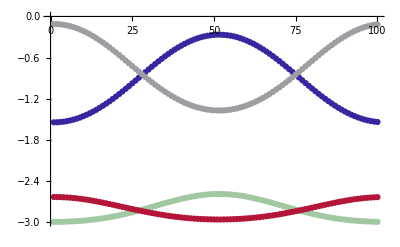

{fem0deg_ISXextended_Blue,fem45deg_ISXextended_Light Green,fem90deg_ISXextended_Red,fem135deg_ISXextended_Gray}

```mathematica
(*spot check to see if plot data are correct*)
ListPlot[TMADATA[[femConditions,;;,LGR,hipL+1]],PlotStyle->colors]
```

```mathematica
filename
```

Figure 4_FE_relativeScaling.png

```mathematica
componentLabel
```

LAR

```mathematica
PP//Length
```

5

```mathematica
Manipulate[PPrel[[i]],{i,1,Length[PPrel],1}]
```

```mathematica
SetDirectory["/Users/chrisrichards/Desktop/FrogWork/FrogPubs/kassinaMJ/Figures/Drafts"];
(*Export["graph_widthScaled.png",g]*)
(*Export["graph_unScaled.png",g]*)
Export["graph_absoluteScaled.png",g]
ResetDirectory[]
```

graph_absoluteScaled.png

/Users/chrisrichards/Desktop/FrogWork/DATA/FrogMJModelling/DATA/Test data/momentarm

```mathematica
ListLinePlot[data,MeshFunctions->{#2&},Mesh->{{-1000,0},{0,1000}},MeshShading->{Thick,Dashed},MeshStyle->None,PlotStyle->Red]
```

0.00168592

```mathematica
(*check to see if all ranges are the same*)
(*
Table[range=(PlotRange/.AbsoluteOptions[PP[[i]],PlotRange])[[2]];
range[[2]]-range[[1]]

,{i,1,Length[PP]}]
*)
```

{0.00168592,0.00168592,0.00168592,0.00168592}

```mathematica
maxWidth
```

0.00168592

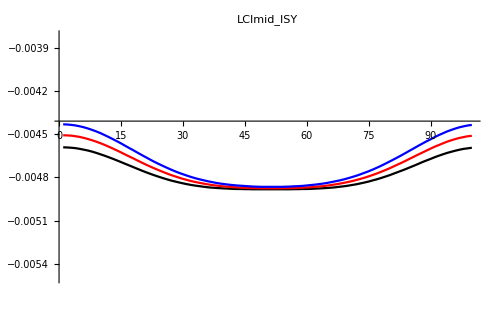

{-0.00488203,0.00486205}

{-0.000852948,0.00083297}

```mathematica
PP[[1]]
```

```mathematica
43
```

```mathematica
p[[1,2,1,3,3]]//First
```

{{1.,-0.003686},{2.,-0.003686},{3.,-0.00368601},{4.,-0.00368505},{5.,-0.00368501},{6.,-0.00368412},{7.,-0.00368312},{8.,-0.00368214},{9.,-0.00368116},{10.,-0.00368018},{11.,-0.0036792},{12.,-0.00367827},{13.,-0.00367647},{14.,-0.00367528},{15.,-0.00367355},{16.,-0.00367232},{17.,-0.00367063},{18.,-0.00366936},{19.,-0.00366772},{20.,-0.00366627},{21.,-0.00366601},{22.,-0.00366535},{23.,-0.00366537},{24.,-0.00366701},{25.,-0.00366884},{26.,-0.00367222},{27.,-0.0036776},{28.,-0.00368502},{29.,-0.00369399},{30.,-0.003695},{31.,-0.00368724},{32.,-0.00368038},{33.,-0.00367353},{34.,-0.00366667},{35.,-0.00365976},{36.,-0.00365323},{37.,-0.00364711},{38.,-0.00364039},{39.,-0.00363482},{40.,-0.00362974},{41.,-0.00362399},{42.,-0.00361911},{43.,-0.00361435},{44.,-0.00361045},{45.,-0.00360664},{46.,-0.00360371},{47.,-0.00360084},{48.,-0.00359889},{49.,-0.00359696},{50.,-0.00359599},{51.,-0.00359501},{52.,-0.00359499},{53.,-0.00359594},{54.,-0.00359691},{55.,-0.0035988},{56.,-0.00360075},{57.,-0.00360358},{58.,-0.00360651},{59.,-0.00361029},{60.,-0.00361419},{61.,-0.00361891},{62.,-0.00362384},{63.,-0.00362868},{64.,-0.00363432},{65.,-0.00364024},{66.,-0.00364606},{67.,-0.00365262},{68.,-0.00365953},{69.,-0.00366638},{70.,-0.00367331},{71.,-0.00367951},{72.,-0.0036859},{73.,-0.00369365},{74.,-0.00369384},{75.,-0.00368545},{76.,-0.00367778},{77.,-0.00367295},{78.,-0.00366954},{79.,-0.00366703},{80.,-0.00366548},{81.,-0.00366488},{82.,-0.0036653},{83.,-0.00366634},{84.,-0.00366727},{85.,-0.00366859},{86.,-0.0036703},{87.,-0.00367147},{88.,-0.00367352},{89.,-0.00367524},{90.,-0.00367639},{91.,-0.00367823},{92.,-0.00367916},{93.,-0.00368014},{94.,-0.00368112},{95.,-0.0036821},{96.,-0.00368308},{97.,-0.00368407},{98.,-0.00368501},{99.,-0.003685},{100.,-0.003686}}

```mathematica
qScaleGraphs
```

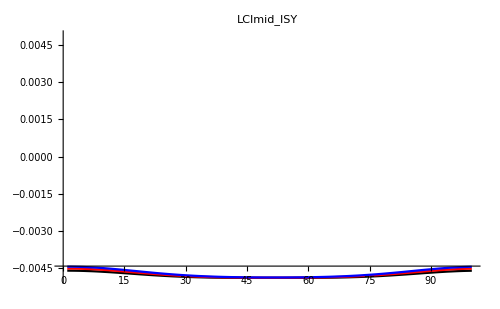

```mathematica
PP[[1]]
```

```mathematica
p[[2]]
```

{DisplayFunction→Identity,PlotRangePadding→{{Scaled[0.02],Scaled[0.02]},{Scaled[0.05],Scaled[0.05]}},AxesOrigin→{0,-0.00192479},PlotRange→{{0.,100.},{-0.003695,-0.00200908}},DisplayFunction→Identity,AspectRatio→1/GoldenRatio,Axes→{True,True},AxesLabel→{None,None},AxesOrigin→{0,-0.00192479},DisplayFunction:>Identity,Frame→{{False,False},{False,False}},FrameLabel→{{None,None},{None,None}},FrameTicks→{{Automatic,Automatic},{Automatic,Automatic}},GridLines→{None,None},GridLinesStyle→Directive[-Graphics-],ImageSize→500,Method→{},PlotLabel→RIL1_ISY,PlotRange→{{0.,100.},{-0.003695,-0.00200908}},PlotRangeClipping→True,PlotRangePadding→{{Scaled[0.02],Scaled[0.02]},{Scaled[0.05],Scaled[0.05]}},Ticks→{Automatic,Automatic}}

{32}

```mathematica
PlotRange/.AbsoluteOptions[PP[[1]],PlotRange]={{0.,20},{-0.003694998816516009,-0.0020090810798183514}};
```

Set::write: Tag ReplaceAll in PlotRange/. {PlotRange → {{0., 100.}, {-0.00488203, -0.00443}}} is Protected.

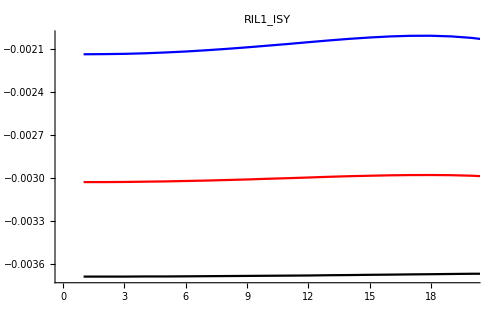

```mathematica
Show[p,PlotRange->{{0,20},All}]
```

```mathematica
p[[2]]
```

{DisplayFunction→Identity,PlotRangePadding→{{Scaled[0.02],Scaled[0.02]},{Scaled[0.05],Scaled[0.05]}},AxesOrigin→{0,-0.00192479},PlotRange→{{0.,100.},{-0.003695,-0.00200908}},DisplayFunction→Identity,AspectRatio→1/GoldenRatio,Axes→{True,True},AxesLabel→{None,None},AxesOrigin→{0,-0.00192479},DisplayFunction:>Identity,Frame→{{False,False},{False,False}},FrameLabel→{{None,None},{None,None}},FrameTicks→{{Automatic,Automatic},{Automatic,Automatic}},GridLines→{None,None},GridLinesStyle→Directive[-Graphics-],ImageSize→500,Method→{},PlotLabel→RIL1_ISY,PlotRange→{{0.,100.},{-0.003695,-0.00200908}},PlotRangeClipping→True,PlotRangePadding→{{Scaled[0.02],Scaled[0.02]},{Scaled[0.05],Scaled[0.05]}},Ticks→{Automatic,Automatic}}

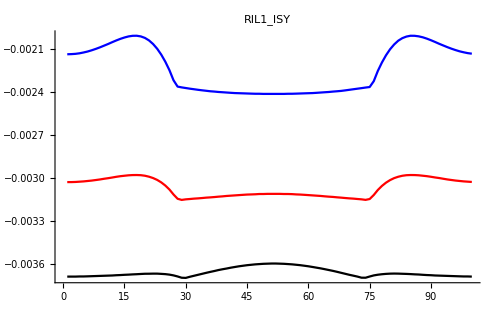

```mathematica
p
```

```mathematica
trials
```

{1,2,3,4}

```mathematica
RIL3
```

```mathematica
muscleGroup
```

{3,4,5,6,7,8,9,10}

LCIprox_LCImid_LCIdist_RCIprox_RCImid_RCIdist

```mathematica
Clear[muscleGroup]
```

{Black:fem0deg_ISXextended,Red:fem45deg_ISXextended,Blue:fem90deg_ISXextended,Green:fem135deg_ISXextended}

RGBColor[1, 0, 0]

```mathematica
(*(*Axial muscle group*)
axialGroupL={"LCIprox","LCImid","LCIdist"};
axialGroupR={"RCIprox","RCImid","RCIdist"};
grouplabel="axialGroupR";
group=ToExpression[grouplabel];*)




P=
Table[

trialgroup=iTEST;
trials=trialsList[[trialgroup]];

dashing=dashings[[trialgroup]];

Table[

muslabel=group[[i]];
mus=ToExpression[muslabel];


colors={Black,Red,Blue,Green};
p1=ListLinePlot[TMADATA[[trials,;;,mus,dof]],PlotLabel->muslabel<>"_"<>jointlabel,PlotStyle->Thread[{colors,Dashing[dashing]}]];
(*p2=ListPlot[TMADATA[[trials,;;,mus,dof+1]],PlotLabel->jointlabel<>"_FE",PlotStyle->colors];
p3=ListPlot[TMADATA[[trials,;;,mus,dof+2]],PlotLabel->jointlabel<>"_AA",PlotStyle->colors];*)
p1
,{i,1,Length[group]}]
,{iTEST,1,3}];
Pout=GraphicsGrid[P,ImageSize->size,PlotLabel->grouplabel]
```

Part::partd: Part specification trialsList ⟦ 1 ⟧ is longer than depth of object.

Part::partd: Part specification trialsList ⟦ 2 ⟧ is longer than depth of object.

General::stop: Further output of Part :: partd will be suppressed during this calculation.

Transpose::nmtx: The first two levels of {} cannot be transposed.

-Graphics-

```mathematica
testNames[[trials]]
```

{fem0deg_ISXfullFlexed,fem45deg_ISXfullFlexed,fem90deg_ISXfullFlexed,fem135deg_ISXfullFlexed}

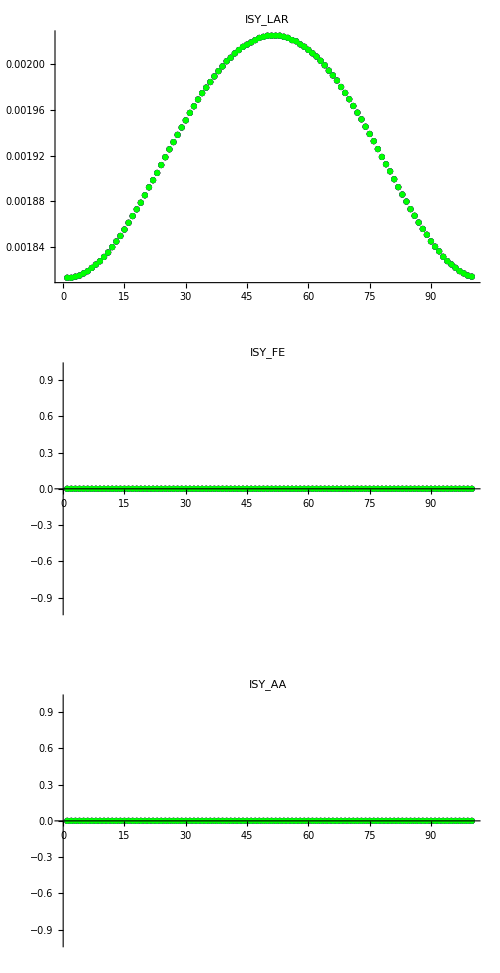
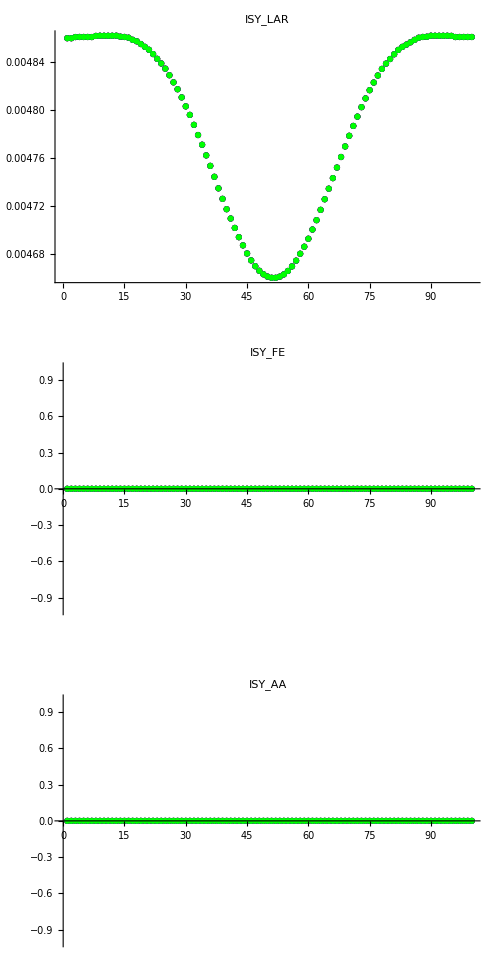
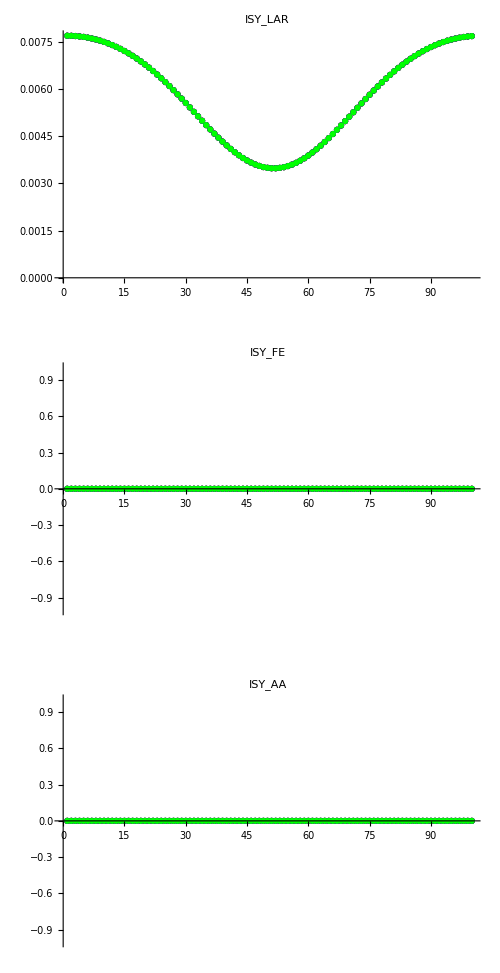

```mathematica
(*Axial muscle group*)
axialGroupL={LCIprox,LCImid,LCIdist};
axialGroupR={RCIprox,RCImid,RCIdist};
trials={{1,2,3,4},{5,6,7,8},{9,10,11,12}}[[1]];
colors={Black,Red,Blue,Green};
grouplabel="axialGroupR";
group=ToExpression[grouplabel];
jointlabel="ISY";
dof=ToExpression[jointlabel];
size=500;
trials={{1,2,3,4},{5,6,7,8},{9,10,11,12}}[[1]];
P=Table[

mus=group[[i]];

colors={Black,Red,Blue,Green};
p1=ListPlot[TMADATA[[trials,;;,mus,dof]],PlotLabel->jointlabel<>"_LAR",PlotStyle->colors];
p2=ListPlot[TMADATA[[trials,;;,mus,dof+1]],PlotLabel->jointlabel<>"_FE",PlotStyle->colors];
p3=ListPlot[TMADATA[[trials,;;,mus,dof+2]],PlotLabel->jointlabel<>"_AA",PlotStyle->colors];
GraphicsColumn[{p1,p2,p3},ImageSize->size,PlotLabel->grouplabel]

,{i,1,Length[group]}];
```

{1,2,3,4}

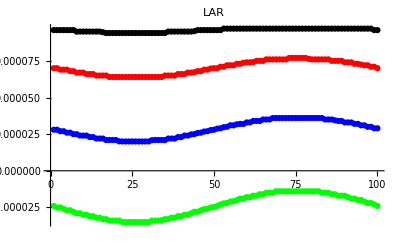

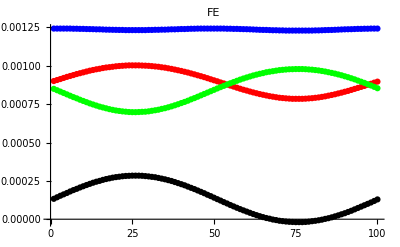

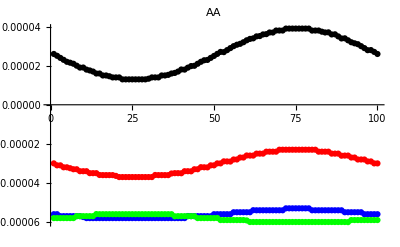

```mathematica
mus=LCR;
dof=hipL;
trials={{1,2,3,4},{5,6,7,8},{9,10,11,12}}[[1]]
colors={Black,Red,Blue,Green};
ListPlot[TMADATA[[trials,;;,mus,dof]],PlotLabel->"LAR",PlotStyle->colors]
ListPlot[TMADATA[[trials,;;,mus,dof+1]],PlotLabel->"FE",PlotStyle->colors]
ListPlot[TMADATA[[trials,;;,mus,dof+2]],PlotLabel->"AA",PlotStyle->colors]
```

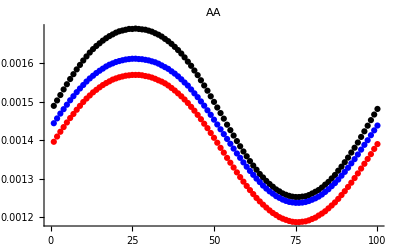

```mathematica
ListPlot[TMADATA[[{1,5,9},;;,LCIdist,ISX+0]],PlotLabel->"AA",PlotStyle->colors]
```

## FIGURE Exemplar Run: Axial, Protractors, Retractors,

```mathematica
(*FIGURE OPTIONS*)
(*Option 1: Exemplar conditions- Axial muscles*)
(*Option 2: Exemplar conditions- Protractors*)
(*Option 3: Exemplar conditions- Retractors*)
(*Option 4: Exemplar conditions- Protractors & Retractors*)
(*Option 5: Exemplar conditions- Misc*)


figOption=5;
figNames={"Figure_RUN_axial", "Figure_RUN_pro", "Figure_RUN_ret","Figure_RUN_pro&ret","Figure_RUN_misc"};
figname=figNames[[figOption]];
size=1000;

qfigExport=True;(*for exporting Figs*)
qExport=False;(*leave false - this is only for exporting raw plots for browsing*)
qScaleGraphs=True;qScaling="relative"(*width*)(*relative*)(*absolute*);(*absolute scaling makes all axes have the same bounds; width scaling makes all graphs have same y axis range, but with offsets appropriate for the data.*)

(*--------- load pelvis icons--------------------*)
(*iconDirectory="/Users/chrisrichards/Desktop/FrogWork/FrogPubs/kassinaMJ";
SetDirectory[iconDirectory];
pelvicLeftIcon=Import["pelvisLeft_icon.png"];
pelvicRightIcon=Import["pelvisRight_icon.png"];
pelvicCenterIcon=Import["pelvisCenter_icon.png"];
ResetDirectory[];*)


topLeftIndex={2,1,1,1,1,1}[[figOption]];(*which number fig to put the icons on*)
(*---------pelvis icons------------------------------*)


(*selecting which portions of muscles to represent*)
LCI=LCIdist;
RCI=RCIdist;
LIL=LIL1;
RIL=RIL1;
LIE=LIEprox;
LAM=LAMcrv;
LII=LIImed;

(*-----------------*)
TMAfileEndings=Table[
str=TMAfiles[[i]];
StringTake[str,{6,8}],{i,1,Length[TMAfiles]}];(*find which files are TST versus RUN*)
TMAexemplarIndices=Position[TMAfileEndings,"RUN"]//Flatten;
TMAexemplars=TMAfiles[[TMAexemplarIndices]];
TMADATAex=TMADATA[[TMAexemplarIndices]];
testNames=TMAexemplars;
(*-----------------*)
timeOfStance=0.657;(*time of stance - fraction of duration - see Kinematics Paper-Walking trial METADATA-AJC mods_modCTR-Version 2.xlsx *)
startSwingIndex=Round[timeOfStance*100];
(*Do[
setIndex=iSet;*)
exportDir="/Users/chrisrichards/Desktop/FrogWork/CODE/mujoco150_KM/output/plots/";


axialGroup={"LCI","LIL","RCI","RIL"};
protractorGroup={"LIE","LSA","LAL","LAM","LII"};
retractorGroup={"LSM","LIFB","LOE","LGR","LIFM"};
miscGroup={"LPY","LGL","LCR"};


femConditions={1,2};
axConditions={1,2};
(*femColors={"Black","Red","Blue","Green"};*)
(*femColors={Black,Red,Blue,Green};*)
axColors={Setting[0.6252689402609293],Setting[0.]};
femColors={Setting[0.6252689402609293],Setting[0.]};
axWeights={0.003,0.008};(*line weights*)
femWeights={0.003,0.008};(*line weights*)
axcolorStr={"Gray","Black"};
femcolorStr={"Gray","Black"};
axialSet={"axialGroup","ISY",axConditions,axColors,axWeights,axcolorStr}; (*NOTE AMBER IS GROUPING IN IL*)
protractorSet={"protractorGroup","hipL",femConditions,femColors,femWeights,femcolorStr};
retractorSet={"retractorGroup","hipL",femConditions,femColors,femWeights,femcolorStr};
proretSet={"proretGroup","hipL",femConditions,femColors,femWeights,femcolorStr};
miscSet={"miscGroup","hipL",femConditions,femColors,femWeights,femcolorStr};
(*ilSet={"ilgroup","ISY",{1,5,9},{"Black","Red","Blue"}};
femProtractionSet={"femProtractionGroup","hipL",{1,2,3,4},{"Black","Red","Blue","Green"}};
femRetractionSet={"femRetractionGroup","hipL",{1,2,3,4},{"Black","Red","Blue","Green"}};
femProtractionAdductionSet={"femProtractionAdductionGroup","hipL",{1,2,3,4},{"Black","Red","Blue","Green"}};
femRetractionAdductionSet={"femRetractionAdductionGroup","hipL",{1,2,3,4},{"Black","Red","Blue","Green"}};
femProtractionAbductionSet={"femProtractionAbductionGroup","hipL",{1,2,3,4},{"Black","Red","Blue","Green"}};
femMiscSet={"femMiscGroup","hipL",{1,2,3,4},{"Black","Red","Blue","Green"}};*)

(*parameterSet={axialSet,ilSet,femProtractionSet,femRetractionSet,femProtractionAdductionSet,femRetractionAdductionSet,femProtractionAbductionSet,femMiscSet}[[setIndex]];*)

(*parameterSet=axialSet;*)


parameterSet={axialSet,protractorSet,retractorSet,proretSet,miscSet}[[figOption]];
qPelvisJoint=parameterSet[[1]]=="axialGroup";
ncomponents=If[qPelvisJoint,1,3];

GG={};(*gather graph grids here*)

Do[(*iterate through joint Components LAR, FE, AA*)
PP={};


jointComponent=ijointComponent;(*0 = LAR, 1 = FE, 2 = AA*);
componentLabel={"LAR","FE","AA"}[[ijointComponent+1]];
componentLabel=If[qPelvisJoint,"LatRotation",componentLabel];
(*parameterSet=protractorSet;*)
musgroup=parameterSet[[1]];
jointlabel=parameterSet[[2]];
trials=parameterSet[[3]];
colorsExpr=parameterSet[[4]];
lineWeights=parameterSet[[5]];
colorStr=parameterSet[[6]];

(*colors=ToExpression[colorStr];*)
(*plot graphics parameters - eventually load these from a file?*)

dashing={0.01,0.02};
colors=colorsExpr;
nplots=Length[trials];
weightStyles=Table[Thickness[lineWeights[[n]]],{n,1,nplots}];
lineStyles=Thread[{colors,weightStyles}];

dof=ToExpression[jointlabel]+jointComponent;
muscleGroup=ToExpression[musgroup];


(*trialsList={{1,2,3,4},{5,6,7,8},{9,10,11,12}};*)



(*dashings={None,0.01,0.05};*)

(*qPelvisJoint=(jointlabel=="ISY"||jointlabel=="ISX");*)


Do[


(*dashing=dashings[[trialgroup]];*)

muslabel=muscleGroup[[iMUS]];
label=muslabel<>"_"<>jointlabel;
mus=ToExpression[muslabel];
dat1=TMADATAex[[trials,;;,mus,dof]];
p1=ListLinePlot[dat1,PlotLabel->label,PlotStyle->colors,ImageSize->size,PlotRange->All];
p=p1;


SetDirectory[exportDir];
If[qExport,
Export[label<>".png",p];
];
ResetDirectory[];
PP=Join[PP,{p}];
(*PrintTemporary[mus]*)
,{iMUS,1,Length[muscleGroup]}];
legendText=Table[
colorStr[[i]]<>":"<>testNames[[trials[[i]]]],{i,1,Length[colorStr]}];
SetDirectory[exportDir];
If[qExport,
Export[musgroup<>"_README.txt",legendText];
];
ResetDirectory[];
(*PrintTemporary[iSet];

,{iSet,1,1}];*)


(*-- scale the plots---*)

If[qScaleGraphs,
If[qScaling=="absolute",
(*first option - scale based on absolute ranges - makes the trends to narrow to see*)

PPunscaled=PP;
xrange=(PlotRange/.AbsoluteOptions[PPunscaled[[1]],PlotRange])[[1]];
yranges=Table[
(PlotRange/.AbsoluteOptions[PPunscaled[[i]],PlotRange])[[2]]


,{i,1,Length[PPunscaled]}];
ymin=Min[yranges[[;;,1]]];
ymax=Max[yranges[[;;,2]]];
yrange={ymin,ymax};
scaledRange={xrange,yrange};



PP=Table[Show[PPunscaled[[i]],PlotRange->scaledRange],{i,1,Length[PP]}];

,
If[qScaling=="width",
(*second option -"width scaling" - scale based on width of each plot - i.e. find the plot with maximim difference between ymin and wmax*) 
(*use this for each plot, but the range is adjusted such that the mean is a bout the mean of the data*)
PPunscaled=PP;
xrange=(PlotRange/.AbsoluteOptions[PP[[1]],PlotRange])[[1]];
yranges=Table[
(PlotRange/.AbsoluteOptions[PP[[i]],PlotRange])[[2]]

,{i,1,Length[PPunscaled]}];
plotWidths=Table[Abs[yranges[[i,1]]-yranges[[i,2]]],{i,1,Length[yranges]}];(*find the "width" i.e. the distance between min and max plot ranges*)
maxWidth=Max[plotWidths];

scaledRanges=Table[
range=(PlotRange/.AbsoluteOptions[PPunscaled[[i]],PlotRange])[[2]];
meanrange=Mean[range];
{meanrange-maxWidth/2,meanrange+maxWidth/2},{i,1,Length[PP]}];
PP=Table[Show[PPunscaled[[i]],PlotRange->scaledRanges[[i]]],{i,1,Length[PP]}];
,
(*third option, "relative" scaling*)
(*where the data are zeroed about the mean, then scaled with an absolute range*)

PPunscaled=PP;
meanVALUES={};(*mean moment arm values for all plots*)
PPrel=Table[
plot=PPunscaled[[i]];
plotDATAraw=Cases[plot,Line[{x__}]->x,∞];(*extract data from plot*)
plotDATA=Partition[plotDATAraw,npoints];(*reshape data to nplots x npoints x 2 *)
(*nplots=Dimensions[plotDATA][[1]];*)
meanValues={};
Do[
allYdata=plotDATA[[j,;;,2]];
offsetY=Mean[Flatten[allYdata]];
meanValues=Join[meanValues,{offsetY}];
allYdataOffset=allYdata-offsetY;
plotDATA[[j,;;,2]]=allYdataOffset;
,{j,1,nplots}];

(*
allYdata=plotDATA[[;;,;;,2]];
offsetY=Mean[Flatten[allYdata]];
meanValues=Join[meanValues,{offsetY}];
allYdataOffset=allYdata-offsetY;
plotDATA[[;;,;;,2]]=allYdataOffset;

*)
label=PlotLabel/.AbsoluteOptions[plot,PlotLabel];
(*make the plot.  Note the Mesh function stuff is to make the plots dashed*)
(*if they are negative wrt to offset*)

(*plotrel=ListLinePlot[plotDATA,PlotStyle->colors,MeshFunctions->{#2&},Mesh->{{-1000,-meanValues[[i]]},{-meanValues[[i]],1000}},MeshShading->{Thick,Dashed},MeshStyle->None,PlotLabel->label,ImageSize->size,PlotRange->All]*)
meanVALUES=Join[meanVALUES,{meanValues}];
plotrel=Show[
Table[
plotcolor=lineStyles[[k,1]];
plotweight=lineStyles[[k,2]];
ListLinePlot[plotDATA[[k]],PlotStyle->plotcolor,MeshFunctions->{#2&},Mesh->{{-1000,-meanValues[[k]]},{-meanValues[[k]],1000}},MeshShading->{plotweight,Directive[plotweight,Dashing[dashing]]},MeshStyle->None,PlotLabel->label,ImageSize->size,BaseStyle->basestyle,AxesStyle->axStyle]
,{k,1,nplots}],
PlotRange->All]


,{i,1,Length[PP]}];


xrange=(PlotRange/.AbsoluteOptions[PPrel[[1]],PlotRange])[[1]];
yranges=Table[
(PlotRange/.AbsoluteOptions[PPrel[[i]],PlotRange])[[2]]


,{i,1,Length[PPrel]}];
ymin=Min[yranges[[;;,1]]];
ymax=Max[yranges[[;;,2]]];
ymaxPadded=ymax+0.2*ymax;(*pad this a little to allow room for text*)
yrange={ymin,ymaxPadded};
scaledRange={xrange,yrange};

pswing=ListLinePlot[{{startSwingIndex,ymin},{startSwingIndex,ymaxPadded}},PlotStyle->{Black,Dashed}];

PP=Table[

(*complicated code to generate box of coloured text values for mean values*)
meanString=vectorToString[meanVALUES[[i]]];
Do[
meanString=StringReplace[meanString,#->ToString[Style[#,colors[[m]]],StandardForm]&/@{ToString[meanVALUES[[i,m]]]}]
,{m,1,nplots}];
meanLabel=Framed[meanString];

iconY=0.8;
If[i==topLeftIndex,
plot1=Show[
PPrel[[i]],PlotRange->scaledRange,Epilog->{
Inset[meanLabel,Scaled[{0.5,0.95}]](*,Inset[pelvicRightIcon,Scaled[{0.1,iconY}],Scaled[{0.5,0.5}],5],
Inset[pelvicCenterIcon,Scaled[{0.5,iconY}],Scaled[{0.5,0.5}],5],
Inset[pelvicLeftIcon,Scaled[{0.9,iconY}],Scaled[{0.5,0.5}],5]*)
}
],
plot1=Show[
PPrel[[i]],PlotRange->scaledRange,Epilog->
Inset[meanLabel,Scaled[{0.5,0.95}]]
]
];
Show[plot1,pswing]


,{i,1,Length[PPrel]}];

](*end If width*)
](*end If absolute*)
](*end If scale*);


(*assemble into grids for final figure*)

g=
If[figOption==1,
(*Partition[PP,2]//Transpose//GraphicsGrid*)
GraphicsGrid[{{PP[[2]],PP[[4]]},{PP[[1]],PP[[3]]}}]
,
If[figOption==2,
GraphicsColumn[PP]
,
If[figOption==3,
GraphicsColumn[PP]
,
If[figOption==4,
Partition[PP,2]//GraphicsGrid
,
If[figOption==5,
GraphicsColumn[PP]
](*end if option 5*)
](*end if option 4*)
](*end if option 3*)
](*end if option 2*)
](*end if option 1*);
GG=Join[GG,{g}];


If[qfigExport,
SetDirectory[exportDir];
filename=figname<>"_"<>componentLabel<>"_"<>qScaling<>"Scaling.png";
Export[filename,g];
ResetDirectory[];
filename
];
Print[filename]
,{ijointComponent,0,ncomponents-1}](*end jointComponent iterator*)

Manipulate[GG[[i]],{i,1,Length[GG],1}]
```

Figure_RUN_misc_LAR_relativeScaling.png

Figure_RUN_misc_FE_relativeScaling.png

Figure_RUN_misc_AA_relativeScaling.png

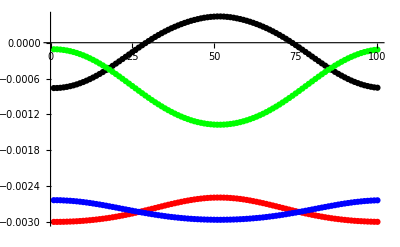

```mathematica
(*spot check to see if plot data are correct*)
ListPlot[TMADATA[[{1,2,3,4},;;,LGR,hipL+1]],PlotStyle->colors]
```

```mathematica
filename
```

Figure 4_FE_relativeScaling.png

```mathematica
componentLabel
```

LAR

```mathematica
PP//Length
```

5

```mathematica
Manipulate[PPrel[[i]],{i,1,Length[PPrel],1}]
```

```mathematica
SetDirectory["/Users/chrisrichards/Desktop/FrogWork/FrogPubs/kassinaMJ/Figures/Drafts"];
(*Export["graph_widthScaled.png",g]*)
(*Export["graph_unScaled.png",g]*)
Export["graph_absoluteScaled.png",g]
ResetDirectory[]
```

graph_absoluteScaled.png

/Users/chrisrichards/Desktop/FrogWork/DATA/FrogMJModelling/DATA/Test data/momentarm

```mathematica
ListLinePlot[data,MeshFunctions->{#2&},Mesh->{{-1000,0},{0,1000}},MeshShading->{Thick,Dashed},MeshStyle->None,PlotStyle->Red]
```

0.00168592

```mathematica
(*check to see if all ranges are the same*)
(*
Table[range=(PlotRange/.AbsoluteOptions[PP[[i]],PlotRange])[[2]];
range[[2]]-range[[1]]

,{i,1,Length[PP]}]
*)
```

{0.00168592,0.00168592,0.00168592,0.00168592}

```mathematica
maxWidth
```

0.00168592

```mathematica
PP[[1]]
```

-Graphics-

{-0.00488203,0.00486205}

{-0.000852948,0.00083297}

```mathematica
43
```

```mathematica
p[[1,2,1,3,3]]//First
```

{{1.,-0.003686},{2.,-0.003686},{3.,-0.00368601},{4.,-0.00368505},{5.,-0.00368501},{6.,-0.00368412},{7.,-0.00368312},{8.,-0.00368214},{9.,-0.00368116},{10.,-0.00368018},{11.,-0.0036792},{12.,-0.00367827},{13.,-0.00367647},{14.,-0.00367528},{15.,-0.00367355},{16.,-0.00367232},{17.,-0.00367063},{18.,-0.00366936},{19.,-0.00366772},{20.,-0.00366627},{21.,-0.00366601},{22.,-0.00366535},{23.,-0.00366537},{24.,-0.00366701},{25.,-0.00366884},{26.,-0.00367222},{27.,-0.0036776},{28.,-0.00368502},{29.,-0.00369399},{30.,-0.003695},{31.,-0.00368724},{32.,-0.00368038},{33.,-0.00367353},{34.,-0.00366667},{35.,-0.00365976},{36.,-0.00365323},{37.,-0.00364711},{38.,-0.00364039},{39.,-0.00363482},{40.,-0.00362974},{41.,-0.00362399},{42.,-0.00361911},{43.,-0.00361435},{44.,-0.00361045},{45.,-0.00360664},{46.,-0.00360371},{47.,-0.00360084},{48.,-0.00359889},{49.,-0.00359696},{50.,-0.00359599},{51.,-0.00359501},{52.,-0.00359499},{53.,-0.00359594},{54.,-0.00359691},{55.,-0.0035988},{56.,-0.00360075},{57.,-0.00360358},{58.,-0.00360651},{59.,-0.00361029},{60.,-0.00361419},{61.,-0.00361891},{62.,-0.00362384},{63.,-0.00362868},{64.,-0.00363432},{65.,-0.00364024},{66.,-0.00364606},{67.,-0.00365262},{68.,-0.00365953},{69.,-0.00366638},{70.,-0.00367331},{71.,-0.00367951},{72.,-0.0036859},{73.,-0.00369365},{74.,-0.00369384},{75.,-0.00368545},{76.,-0.00367778},{77.,-0.00367295},{78.,-0.00366954},{79.,-0.00366703},{80.,-0.00366548},{81.,-0.00366488},{82.,-0.0036653},{83.,-0.00366634},{84.,-0.00366727},{85.,-0.00366859},{86.,-0.0036703},{87.,-0.00367147},{88.,-0.00367352},{89.,-0.00367524},{90.,-0.00367639},{91.,-0.00367823},{92.,-0.00367916},{93.,-0.00368014},{94.,-0.00368112},{95.,-0.0036821},{96.,-0.00368308},{97.,-0.00368407},{98.,-0.00368501},{99.,-0.003685},{100.,-0.003686}}

```mathematica
qScaleGraphs
```

```mathematica
PP[[1]]
```

-Graphics-

```mathematica
p[[2]]
```

{DisplayFunction→Identity,PlotRangePadding→{{Scaled[0.02],Scaled[0.02]},{Scaled[0.05],Scaled[0.05]}},AxesOrigin→{0,-0.00192479},PlotRange→{{0.,100.},{-0.003695,-0.00200908}},DisplayFunction→Identity,AspectRatio→1/GoldenRatio,Axes→{True,True},AxesLabel→{None,None},AxesOrigin→{0,-0.00192479},DisplayFunction:>Identity,Frame→{{False,False},{False,False}},FrameLabel→{{None,None},{None,None}},FrameTicks→{{Automatic,Automatic},{Automatic,Automatic}},GridLines→{None,None},GridLinesStyle→Directive[-Graphics-],ImageSize→500,Method→{},PlotLabel→RIL1_ISY,PlotRange→{{0.,100.},{-0.003695,-0.00200908}},PlotRangeClipping→True,PlotRangePadding→{{Scaled[0.02],Scaled[0.02]},{Scaled[0.05],Scaled[0.05]}},Ticks→{Automatic,Automatic}}

{32}

```mathematica
PlotRange/.AbsoluteOptions[PP[[1]],PlotRange]={{0.,20},{-0.003694998816516009,-0.0020090810798183514}};
```

Set::write: Tag ReplaceAll in PlotRange/. {PlotRange → {{0., 100.}, {-0.00488203, -0.00443}}} is Protected.

```mathematica
Show[p,PlotRange->{{0,20},All}]
```

-Graphics-

```mathematica
p[[2]]
```

{DisplayFunction→Identity,PlotRangePadding→{{Scaled[0.02],Scaled[0.02]},{Scaled[0.05],Scaled[0.05]}},AxesOrigin→{0,-0.00192479},PlotRange→{{0.,100.},{-0.003695,-0.00200908}},DisplayFunction→Identity,AspectRatio→1/GoldenRatio,Axes→{True,True},AxesLabel→{None,None},AxesOrigin→{0,-0.00192479},DisplayFunction:>Identity,Frame→{{False,False},{False,False}},FrameLabel→{{None,None},{None,None}},FrameTicks→{{Automatic,Automatic},{Automatic,Automatic}},GridLines→{None,None},GridLinesStyle→Directive[-Graphics-],ImageSize→500,Method→{},PlotLabel→RIL1_ISY,PlotRange→{{0.,100.},{-0.003695,-0.00200908}},PlotRangeClipping→True,PlotRangePadding→{{Scaled[0.02],Scaled[0.02]},{Scaled[0.05],Scaled[0.05]}},Ticks→{Automatic,Automatic}}

```mathematica
p
```

-Graphics-

```mathematica
trials
```

{1,2,3,4}

```mathematica
RIL3
```

```mathematica
muscleGroup
```

{3,4,5,6,7,8,9,10}

LCIprox_LCImid_LCIdist_RCIprox_RCImid_RCIdist

```mathematica
Clear[muscleGroup]
```

{Black:fem0deg_ISXextended,Red:fem45deg_ISXextended,Blue:fem90deg_ISXextended,Green:fem135deg_ISXextended}

RGBColor[1, 0, 0]

```mathematica
(*(*Axial muscle group*)
axialGroupL={"LCIprox","LCImid","LCIdist"};
axialGroupR={"RCIprox","RCImid","RCIdist"};
grouplabel="axialGroupR";
group=ToExpression[grouplabel];*)




P=
Table[

trialgroup=iTEST;
trials=trialsList[[trialgroup]];

dashing=dashings[[trialgroup]];

Table[

muslabel=group[[i]];
mus=ToExpression[muslabel];


colors={Black,Red,Blue,Green};
p1=ListLinePlot[TMADATA[[trials,;;,mus,dof]],PlotLabel->muslabel<>"_"<>jointlabel,PlotStyle->Thread[{colors,Dashing[dashing]}]];
(*p2=ListPlot[TMADATA[[trials,;;,mus,dof+1]],PlotLabel->jointlabel<>"_FE",PlotStyle->colors];
p3=ListPlot[TMADATA[[trials,;;,mus,dof+2]],PlotLabel->jointlabel<>"_AA",PlotStyle->colors];*)
p1
,{i,1,Length[group]}]
,{iTEST,1,3}];
Pout=GraphicsGrid[P,ImageSize->size,PlotLabel->grouplabel]
```

Part::partd: Part specification trialsList ⟦ 1 ⟧ is longer than depth of object.

Part::partd: Part specification trialsList ⟦ 2 ⟧ is longer than depth of object.

General::stop: Further output of Part :: partd will be suppressed during this calculation.

Transpose::nmtx: The first two levels of {} cannot be transposed.

-Graphics-

```mathematica
testNames[[trials]]
```

{fem0deg_ISXfullFlexed,fem45deg_ISXfullFlexed,fem90deg_ISXfullFlexed,fem135deg_ISXfullFlexed}

```mathematica
(*Axial muscle group*)
axialGroupL={LCIprox,LCImid,LCIdist};
axialGroupR={RCIprox,RCImid,RCIdist};
trials={{1,2,3,4},{5,6,7,8},{9,10,11,12}}[[1]];
colors={Black,Red,Blue,Green};
grouplabel="axialGroupR";
group=ToExpression[grouplabel];
jointlabel="ISY";
dof=ToExpression[jointlabel];
size=500;
trials={{1,2,3,4},{5,6,7,8},{9,10,11,12}}[[1]];
P=Table[

mus=group[[i]];

colors={Black,Red,Blue,Green};
p1=ListPlot[TMADATA[[trials,;;,mus,dof]],PlotLabel->jointlabel<>"_LAR",PlotStyle->colors];
p2=ListPlot[TMADATA[[trials,;;,mus,dof+1]],PlotLabel->jointlabel<>"_FE",PlotStyle->colors];
p3=ListPlot[TMADATA[[trials,;;,mus,dof+2]],PlotLabel->jointlabel<>"_AA",PlotStyle->colors];
GraphicsColumn[{p1,p2,p3},ImageSize->size,PlotLabel->grouplabel]

,{i,1,Length[group]}];
```

{-Graphics-,-Graphics-,-Graphics-}

```mathematica
mus=LCR;
dof=hipL;
trials={{1,2,3,4},{5,6,7,8},{9,10,11,12}}[[1]]
colors={Black,Red,Blue,Green};
ListPlot[TMADATA[[trials,;;,mus,dof]],PlotLabel->"LAR",PlotStyle->colors]
ListPlot[TMADATA[[trials,;;,mus,dof+1]],PlotLabel->"FE",PlotStyle->colors]
ListPlot[TMADATA[[trials,;;,mus,dof+2]],PlotLabel->"AA",PlotStyle->colors]
```

{1,2,3,4}

-Graphics-

-Graphics-

-Graphics-

```mathematica
ListPlot[TMADATA[[{1,5,9},;;,LCIdist,ISX+0]],PlotLabel->"AA",PlotStyle->colors]
```

-Graphics-

## DATA SAVE - Hypothetical Conditions: Axial, Protractors, Retractors

```mathematica
(*FIGURE OPTIONS*)
(*Option 1: Hypothetical conditions- Axial muscles*)
(*Option 2: Hypothetical conditions- Protractors*)
(*Option 3: Hypothetical conditions- Retractors*)
(*Option 4: Hypothetical conditions- Protractors & Retractors*)
(*Option 5: Hypothetical conditions- Misc*)

(*select which one for different data sets*)
figOption=5(*only select 1,4,5 !!!*)
figNames={"Figure_HYP_axial", "Figure_HYP_pro", "Figure_HYP_ret","Figure_HYP_pro&ret","Figure_HYP_misc"};
figname=figNames[[figOption]];

size=500;
qfigExport=qdataExport=True;(*for exporting Figs or data*)
qExport=False;(*leave false - this is only for exporting raw plots for browsing*)
qScaleGraphs=True;qScaling="relative"(*width*)(*relative*)(*absolute*);(*absolute scaling makes all axes have the same bounds; width scaling makes all graphs have same y axis range, but with offsets appropriate for the data.*)
(*relative scaling changes the y values such that they are showing change relative to a reference value, in this case the mean*)

(*--------- load pelvis icons--------------------*)
iconDirectory="/Users/chrisrichards/Desktop/FrogWork/FrogPubs/kassinaMJ";
SetDirectory[iconDirectory];
pelvicLeftIcon=Import["pelvisLeft_icon.png"];
pelvicRightIcon=Import["pelvisRight_icon.png"];
pelvicCenterIcon=Import["pelvisCenter_icon.png"];
ResetDirectory[];


topLeftIndex={2,1,1,1,1,1}[[figOption]];(*which number fig to put the icons on*)
(*---------pelvis icons------------------------------*)


(*(*selecting which portions of muscles to represent*)
LIE=LIEprox;
LAM=LAMcrv;
LII=LIIlat;
*)


(*Do[
setIndex=iSet;*)
exportDir="/Users/chrisrichards/Desktop/FrogWork/CODE/mujoco150_KM/output/plots/";
testNames=
{
"fem10deg_ISXextended","fem45deg_ISXextended","fem90deg_ISXextended","fem135deg_ISXextended",
"fem10deg_ISXhalfFlexed","fem45deg_ISXhalfFlexed","fem90deg_ISXhalfFlexed","fem135deg_ISXhalfFlexed",
"fem10deg_ISXfullFlexed","fem45deg_ISXfullFlexed","fem90deg_ISXfullFlexed","fem135deg_ISXfullFlexed"
};
axialGroup={"LCIprox","LCImid","LCIdist","RCIprox","RCImid","RCIdist","LIL0","LIL1","LIL2","LIL3","RIL0","RIL1","RIL2","RIL3"};
(*axialGroup={"LCImid","LIL1","RCImid","RIL1"};*)
protractorGroup={"LIEprox","LIEdist","LSA","LAL","LAMcrv","LAMstr","LIIlat","LIImed"};
retractorGroup={"LSM","LIFB","LOE","LGR","LIFM"};
proretGroup=Join[protractorGroup,retractorGroup];(*protractorsand retractors together*)
miscGroup={"LPY","LGL","LCR"};

(*axialGroupL={"LCIprox","LCImid","LCIdist"};
axialGroupR={"RCIprox","RCImid","RCIdist"};
ilgroup={"LIL0","LIL1","LIL2","LIL3","RIL0","RIL1","RIL2","RIL3"};
femProtractionGroup={"LIEprox","LIEdist"};
femRetractionGroup={"LSM","LIFB","LOE"};
femProtractionAdductionGroup={"LSA","LAL","LAMcrv","LAMstr"};
femRetractionAdductionGroup={"LGR","LIFM"};
femProtractionAbductionGroup={"LIIlat","LIImed"};
femMiscGroup={"LPY","LGR","LCR"};*)

femConditions={1,2,3,4};
axConditions={1,5,9};
(*femColors={"Black","Red","Blue","Green"};*)
(*femColors={Black,Red,Blue,Green};*)
axColors={Setting[0.21135271229114214],Setting[0.6317998016327153],Setting[0.7024490730144197]};
femColors={Setting[0.21135271229114214],Setting[0.6317998016327153],Setting[0.7024490730144197],Setting[0.6252689402609293]};
axWeights={0.008,0.008,0.003};(*line weights*)
femWeights={0.008,0.008,0.003,0.003};(*line weights*)
axcolorStr={"Blue","Light Green","Red"};
femcolorStr={"Blue","Light Green","Red","Gray"};
axialSet={"axialGroup","ISY",axConditions,axColors,axWeights,axcolorStr}; (*NOTE AMBER IS GROUPING IN IL*)
protractorSet={"protractorGroup","hipL",femConditions,femColors,femWeights,femcolorStr};
retractorSet={"retractorGroup","hipL",femConditions,femColors,femWeights,femcolorStr};
proretSet={"proretGroup","hipL",femConditions,femColors,femWeights,femcolorStr};
miscSet={"miscGroup","hipL",femConditions,femColors,femWeights,femcolorStr};
(*ilSet={"ilgroup","ISY",{1,5,9},{"Black","Red","Blue"}};
femProtractionSet={"femProtractionGroup","hipL",{1,2,3,4},{"Black","Red","Blue","Green"}};
femRetractionSet={"femRetractionGroup","hipL",{1,2,3,4},{"Black","Red","Blue","Green"}};
femProtractionAdductionSet={"femProtractionAdductionGroup","hipL",{1,2,3,4},{"Black","Red","Blue","Green"}};
femRetractionAdductionSet={"femRetractionAdductionGroup","hipL",{1,2,3,4},{"Black","Red","Blue","Green"}};
femProtractionAbductionSet={"femProtractionAbductionGroup","hipL",{1,2,3,4},{"Black","Red","Blue","Green"}};
femMiscSet={"femMiscGroup","hipL",{1,2,3,4},{"Black","Red","Blue","Green"}};*)

(*parameterSet={axialSet,ilSet,femProtractionSet,femRetractionSet,femProtractionAdductionSet,femRetractionAdductionSet,femProtractionAbductionSet,femMiscSet}[[setIndex]];*)

(*parameterSet=axialSet;*)


parameterSet={axialSet,protractorSet,retractorSet,proretSet,miscSet}[[figOption]];
qPelvisJoint=parameterSet[[1]]=="axialGroup";
ncomponents=If[qPelvisJoint,1,3];

GG={};(*gather graph grids here*)

Do[(*iterate through joint Components LAR, FE, AA*)
PP={};


jointComponent=ijointComponent;(*0 = LAR, 1 = FE, 2 = AA*);
componentLabel={"LAR","FE","AA"}[[ijointComponent+1]];
componentLabel=If[qPelvisJoint,"LatRotation",componentLabel];
(*parameterSet=protractorSet;*)
musgroup=parameterSet[[1]];
jointlabel=parameterSet[[2]];
trials=parameterSet[[3]];
colorsExpr=parameterSet[[4]];
lineWeights=parameterSet[[5]];
colorStr=parameterSet[[6]];

(*colors=ToExpression[colorStr];*)
(*plot graphics parameters - eventually load these from a file?*)

dashing={0.01,0.02};
colors=colorsExpr;
nplots=Length[trials];
weightStyles=Table[Thickness[lineWeights[[n]]],{n,1,nplots}];
lineStyles=Thread[{colors,weightStyles}];

dof=ToExpression[jointlabel]+jointComponent;
muscleGroup=ToExpression[musgroup];


(*trialsList={{1,2,3,4},{5,6,7,8},{9,10,11,12}};*)



(*dashings={None,0.01,0.05};*)

(*qPelvisJoint=(jointlabel=="ISY"||jointlabel=="ISX");*)


Do[


(*dashing=dashings[[trialgroup]];*)

muslabel=muscleGroup[[iMUS]];
label=muslabel<>"_"<>jointlabel;
mus=ToExpression[muslabel];
dat1=TMADATA[[trials,;;,mus,dof]];
p1=ListLinePlot[dat1,PlotLabel->label,PlotStyle->colors,ImageSize->size,PlotRange->All];
p=p1;


SetDirectory[exportDir];
If[qExport,
Export[label<>".png",p];
];
ResetDirectory[];
PP=Join[PP,{p}];
(*PrintTemporary[mus]*)
,{iMUS,1,Length[muscleGroup]}];
legendText=Table[
colorStr[[i]]<>":"<>testNames[[trials[[i]]]],{i,1,Length[colorStr]}];
SetDirectory[exportDir];
If[qExport,
Export[musgroup<>"_README.txt",legendText];
];
ResetDirectory[];
(*PrintTemporary[iSet];

,{iSet,1,1}];*)


(*-- scale the plots---*)

If[qScaleGraphs,
If[qScaling=="absolute",
(*first option - scale based on absolute ranges - makes the trends to narrow to see*)
dataoutputfolder=dataoutputroot<>"absoluteScaling/";
PPunscaled=PP;
xrange=(PlotRange/.AbsoluteOptions[PPunscaled[[1]],PlotRange])[[1]];
yranges=Table[
(PlotRange/.AbsoluteOptions[PPunscaled[[i]],PlotRange])[[2]]


,{i,1,Length[PPunscaled]}];
ymin=Min[yranges[[;;,1]]];
ymax=Max[yranges[[;;,2]]];
yrange={ymin,ymax};
scaledRange={xrange,yrange};



PP=Table[Show[PPunscaled[[i]],PlotRange->scaledRange],{i,1,Length[PP]}];
(*--- exporting---*)

If[qdataExport,
SetDirectory[dataoutputfolder];
Do[(*do for each plot in PP*)
plot=PP[[iabsolute]];
label=PlotLabel/.AbsoluteOptions[plot,PlotLabel];
plotDATAraw=Cases[plot,Line[{x__}]->x,∞];(*extract data from plot*)
plotDATA=Partition[plotDATAraw,npoints];
Do[(*do for each line in the plots*)
exportdata=plotDATA[[jabsolute,;;,2]];
conditionName=testNames[[trials[[jabsolute]]]];
filename=figname<>"_"<>label<>"_"<>conditionName<>"_"<>componentLabel<>".csv";
Export[filename,exportdata];
,{jabsolute,1,nplots}];

,{iabsolute,1,Length[PP]}];
ResetDirectory[];
]
(*--- -------*)

,
If[qScaling=="width",
(*second option -"width scaling" - scale based on width of each plot - i.e. find the plot with maximim difference between ymin and wmax*) 
(*use this for each plot, but the range is adjusted such that the mean is a bout the mean of the data*)
PPunscaled=PP;
xrange=(PlotRange/.AbsoluteOptions[PP[[1]],PlotRange])[[1]];
yranges=Table[
(PlotRange/.AbsoluteOptions[PP[[i]],PlotRange])[[2]]

,{i,1,Length[PPunscaled]}];
plotWidths=Table[Abs[yranges[[i,1]]-yranges[[i,2]]],{i,1,Length[yranges]}];(*find the "width" i.e. the distance between min and max plot ranges*)
maxWidth=Max[plotWidths];

scaledRanges=Table[
range=(PlotRange/.AbsoluteOptions[PPunscaled[[i]],PlotRange])[[2]];
meanrange=Mean[range];
{meanrange-maxWidth/2,meanrange+maxWidth/2},{i,1,Length[PP]}];
PP=Table[Show[PPunscaled[[i]],PlotRange->scaledRanges[[i]]],{i,1,Length[PP]}];
,
(*third option, "relative" scaling*)
(*where the data are zeroed about the mean, then scaled with an absolute range*)
dataoutputfolder=dataoutputroot<>"relativeScaling/";

PPunscaled=PP;
meanVALUES={};(*mean moment arm values for all plots*)
PPrel=Table[
plot=PPunscaled[[i]];
plotDATAraw=Cases[plot,Line[{x__}]->x,∞];(*extract data from plot*)
plotDATA=Partition[plotDATAraw,npoints];(*reshape data to nplots x npoints x 2.  Note these are XY pairs*)
(*nplots=Dimensions[plotDATA][[1]];*)
meanValues={};
Do[
allYdata=plotDATA[[j,;;,2]];
offsetY=Mean[Flatten[allYdata]];
meanValues=Join[meanValues,{offsetY}];
allYdataOffset=allYdata-offsetY;
plotDATA[[j,;;,2]]=allYdataOffset;
,{j,1,nplots}];
label=PlotLabel/.AbsoluteOptions[plot,PlotLabel];
(*------Export data---------*)
If[
qdataExport,
SetDirectory[dataoutputfolder];
Do[(*do for each of plot lines*)
exportdata=plotDATA[[itrplot,;;,2]];
conditionName=testNames[[trials[[itrplot]]]];
filename=figname<>"_"<>label<>"_"<>conditionName<>"_"<>componentLabel<>".csv";
Export[filename,exportdata];

,{itrplot,1,nplots}]
ResetDirectory[];
];
(*-------------------------*)


(*
allYdata=plotDATA[[;;,;;,2]];
offsetY=Mean[Flatten[allYdata]];
meanValues=Join[meanValues,{offsetY}];
allYdataOffset=allYdata-offsetY;
plotDATA[[;;,;;,2]]=allYdataOffset;

*)

(*make the plot.  Note the Mesh function stuff is to make the plots dashed*)
(*if they are negative wrt to offset*)

(*plotrel=ListLinePlot[plotDATA,PlotStyle->colors,MeshFunctions->{#2&},Mesh->{{-1000,-meanValues[[i]]},{-meanValues[[i]],1000}},MeshShading->{Thick,Dashed},MeshStyle->None,PlotLabel->label,ImageSize->size,PlotRange->All]*)
meanVALUES=Join[meanVALUES,{meanValues}];
plotrel=Show[Table[
plotcolor=lineStyles[[k,1]];
plotweight=lineStyles[[k,2]];
ListLinePlot[plotDATA[[k]],PlotStyle->plotcolor,MeshFunctions->{#2&},Mesh->{{-1000,-meanValues[[k]]},{-meanValues[[k]],1000}},MeshShading->{plotweight,Directive[plotweight,Dashing[dashing]]},MeshStyle->None,PlotLabel->label,ImageSize->size,BaseStyle->basestyle,AxesStyle->axStyle]
,{k,1,nplots}],PlotRange->All]


,{i,1,Length[PP]}];


xrange=(PlotRange/.AbsoluteOptions[PPrel[[1]],PlotRange])[[1]];
yranges=Table[
(PlotRange/.AbsoluteOptions[PPrel[[i]],PlotRange])[[2]]


,{i,1,Length[PPrel]}];
ymin=Min[yranges[[;;,1]]];
ymax=Max[yranges[[;;,2]]];
yrange={ymin,ymax+0.2*ymax(*pad this a little to allow room for text*)};
scaledRange={xrange,yrange};



PP=Table[

(*complicated code to generate box of coloured text values for mean values*)
meanString=vectorToString[meanVALUES[[i]]];
Do[
meanString=StringReplace[meanString,#->ToString[Style[#,colors[[m]]],StandardForm]&/@{ToString[meanVALUES[[i,m]]]}]
,{m,1,nplots}];
meanLabel=Framed[meanString];

iconY=0.8;
If[i==topLeftIndex,
Show[PPrel[[i]],PlotRange->scaledRange,Epilog->{
Inset[meanLabel,Scaled[{0.5,0.95}]],Inset[pelvicRightIcon,Scaled[{0.1,iconY}],Scaled[{0.5,0.5}],5],
Inset[pelvicCenterIcon,Scaled[{0.5,iconY}],Scaled[{0.5,0.5}],5],
Inset[pelvicLeftIcon,Scaled[{0.9,iconY}],Scaled[{0.5,0.5}],5]
}],
Show[PPrel[[i]],PlotRange->scaledRange,Epilog->
Inset[meanLabel,Scaled[{0.5,0.95}]]]
]

,{i,1,Length[PPrel]}];

](*end If width*)
](*end If absolute*)
](*end If scale*);


(*assemble into grids for final figure*)

g=
If[figOption==1,
(*Partition[PP,2]//Transpose//GraphicsGrid*)
GraphicsGrid[{{PP[[2]],PP[[4]]},{PP[[1]],PP[[3]]}}]
,
If[figOption==2,
GraphicsColumn[PP]
,
If[figOption==3,
GraphicsColumn[PP]
,
If[figOption==4,
Partition[PP,2]//GraphicsGrid
,
If[figOption==5,
GraphicsColumn[PP]
](*end if option 5*)
](*end if option 4*)
](*end if option 3*)
](*end if option 2*)
](*end if option 1*);
GG=Join[GG,{g}];


(*If[qfigExport,
SetDirectory[dataoutputfolder];
filename=figname<>"_"<>componentLabel<>"_"<>qScaling<>"Scaling.png";
(*(*Export[filename,g];*)
(*textREADME=Table[testNames[[trials[[i]]]]<>"_"<>colorStr[[i]],{i,1,Length[trials]}];
fignameREADME=figname<>"_"<>componentLabel<>"_README.txt";
dashingNotes="Solid = positive moment arm = extension || Dashed = negative moment arm = flexion";
textREADME=Join[textREADME,{dashingNotes}];
Export[fignameREADME,textREADME];*)*)
ResetDirectory[];
filename
];*)
Print[filename]
,{ijointComponent,0,ncomponents-1}](*end jointComponent iterator*)
```

5

Figure_HYP_misc_LCR_hipL_fem135deg_ISXextended_LAR.csv

Figure_HYP_misc_LCR_hipL_fem135deg_ISXextended_FE.csv

Figure_HYP_misc_LCR_hipL_fem135deg_ISXextended_AA.csv

testText.txt

```mathematica
Directory[]
```

```mathematica
femConditions
```

{1,2,3,4}

```mathematica
(*spot check to see if plot data are correct*)
ListPlot[TMADATA[[femConditions,;;,LGR,hipL+1]],PlotStyle->colors]
```

-Graphics-

{fem0deg_ISXextended_Blue,fem45deg_ISXextended_Light Green,fem90deg_ISXextended_Red,fem135deg_ISXextended_Gray}

```mathematica
filename
```

Figure 4_FE_relativeScaling.png

```mathematica
componentLabel
```

LAR

```mathematica
PP//Length
```

5

```mathematica
Manipulate[PPrel[[i]],{i,1,Length[PPrel],1}]
```

```mathematica
SetDirectory["/Users/chrisrichards/Desktop/FrogWork/FrogPubs/kassinaMJ/Figures/Drafts"];
(*Export["graph_widthScaled.png",g]*)
(*Export["graph_unScaled.png",g]*)
Export["graph_absoluteScaled.png",g]
ResetDirectory[]
```

graph_absoluteScaled.png

/Users/chrisrichards/Desktop/FrogWork/DATA/FrogMJModelling/DATA/Test data/momentarm

```mathematica
ListLinePlot[data,MeshFunctions->{#2&},Mesh->{{-1000,0},{0,1000}},MeshShading->{Thick,Dashed},MeshStyle->None,PlotStyle->Red]
```

0.00168592

```mathematica
(*check to see if all ranges are the same*)
(*
Table[range=(PlotRange/.AbsoluteOptions[PP[[i]],PlotRange])[[2]];
range[[2]]-range[[1]]

,{i,1,Length[PP]}]
*)
```

{0.00168592,0.00168592,0.00168592,0.00168592}

```mathematica
maxWidth
```

0.00168592

```mathematica
PP[[1]]
```

-Graphics-

{-0.00488203,0.00486205}

{-0.000852948,0.00083297}

```mathematica
43
```

```mathematica
p[[1,2,1,3,3]]//First
```

{{1.,-0.003686},{2.,-0.003686},{3.,-0.00368601},{4.,-0.00368505},{5.,-0.00368501},{6.,-0.00368412},{7.,-0.00368312},{8.,-0.00368214},{9.,-0.00368116},{10.,-0.00368018},{11.,-0.0036792},{12.,-0.00367827},{13.,-0.00367647},{14.,-0.00367528},{15.,-0.00367355},{16.,-0.00367232},{17.,-0.00367063},{18.,-0.00366936},{19.,-0.00366772},{20.,-0.00366627},{21.,-0.00366601},{22.,-0.00366535},{23.,-0.00366537},{24.,-0.00366701},{25.,-0.00366884},{26.,-0.00367222},{27.,-0.0036776},{28.,-0.00368502},{29.,-0.00369399},{30.,-0.003695},{31.,-0.00368724},{32.,-0.00368038},{33.,-0.00367353},{34.,-0.00366667},{35.,-0.00365976},{36.,-0.00365323},{37.,-0.00364711},{38.,-0.00364039},{39.,-0.00363482},{40.,-0.00362974},{41.,-0.00362399},{42.,-0.00361911},{43.,-0.00361435},{44.,-0.00361045},{45.,-0.00360664},{46.,-0.00360371},{47.,-0.00360084},{48.,-0.00359889},{49.,-0.00359696},{50.,-0.00359599},{51.,-0.00359501},{52.,-0.00359499},{53.,-0.00359594},{54.,-0.00359691},{55.,-0.0035988},{56.,-0.00360075},{57.,-0.00360358},{58.,-0.00360651},{59.,-0.00361029},{60.,-0.00361419},{61.,-0.00361891},{62.,-0.00362384},{63.,-0.00362868},{64.,-0.00363432},{65.,-0.00364024},{66.,-0.00364606},{67.,-0.00365262},{68.,-0.00365953},{69.,-0.00366638},{70.,-0.00367331},{71.,-0.00367951},{72.,-0.0036859},{73.,-0.00369365},{74.,-0.00369384},{75.,-0.00368545},{76.,-0.00367778},{77.,-0.00367295},{78.,-0.00366954},{79.,-0.00366703},{80.,-0.00366548},{81.,-0.00366488},{82.,-0.0036653},{83.,-0.00366634},{84.,-0.00366727},{85.,-0.00366859},{86.,-0.0036703},{87.,-0.00367147},{88.,-0.00367352},{89.,-0.00367524},{90.,-0.00367639},{91.,-0.00367823},{92.,-0.00367916},{93.,-0.00368014},{94.,-0.00368112},{95.,-0.0036821},{96.,-0.00368308},{97.,-0.00368407},{98.,-0.00368501},{99.,-0.003685},{100.,-0.003686}}

```mathematica
qScaleGraphs
```

```mathematica
PP[[1]]
```

-Graphics-

```mathematica
p[[2]]
```

{DisplayFunction→Identity,PlotRangePadding→{{Scaled[0.02],Scaled[0.02]},{Scaled[0.05],Scaled[0.05]}},AxesOrigin→{0,-0.00192479},PlotRange→{{0.,100.},{-0.003695,-0.00200908}},DisplayFunction→Identity,AspectRatio→1/GoldenRatio,Axes→{True,True},AxesLabel→{None,None},AxesOrigin→{0,-0.00192479},DisplayFunction:>Identity,Frame→{{False,False},{False,False}},FrameLabel→{{None,None},{None,None}},FrameTicks→{{Automatic,Automatic},{Automatic,Automatic}},GridLines→{None,None},GridLinesStyle→Directive[-Graphics-],ImageSize→500,Method→{},PlotLabel→RIL1_ISY,PlotRange→{{0.,100.},{-0.003695,-0.00200908}},PlotRangeClipping→True,PlotRangePadding→{{Scaled[0.02],Scaled[0.02]},{Scaled[0.05],Scaled[0.05]}},Ticks→{Automatic,Automatic}}

{32}

```mathematica
PlotRange/.AbsoluteOptions[PP[[1]],PlotRange]={{0.,20},{-0.003694998816516009,-0.0020090810798183514}};
```

Set::write: Tag ReplaceAll in PlotRange/. {PlotRange → {{0., 100.}, {-0.00488203, -0.00443}}} is Protected.

```mathematica
Show[p,PlotRange->{{0,20},All}]
```

-Graphics-

```mathematica
p[[2]]
```

{DisplayFunction→Identity,PlotRangePadding→{{Scaled[0.02],Scaled[0.02]},{Scaled[0.05],Scaled[0.05]}},AxesOrigin→{0,-0.00192479},PlotRange→{{0.,100.},{-0.003695,-0.00200908}},DisplayFunction→Identity,AspectRatio→1/GoldenRatio,Axes→{True,True},AxesLabel→{None,None},AxesOrigin→{0,-0.00192479},DisplayFunction:>Identity,Frame→{{False,False},{False,False}},FrameLabel→{{None,None},{None,None}},FrameTicks→{{Automatic,Automatic},{Automatic,Automatic}},GridLines→{None,None},GridLinesStyle→Directive[-Graphics-],ImageSize→500,Method→{},PlotLabel→RIL1_ISY,PlotRange→{{0.,100.},{-0.003695,-0.00200908}},PlotRangeClipping→True,PlotRangePadding→{{Scaled[0.02],Scaled[0.02]},{Scaled[0.05],Scaled[0.05]}},Ticks→{Automatic,Automatic}}

```mathematica
p
```

-Graphics-

```mathematica
trials
```

{1,2,3,4}

```mathematica
RIL3
```

```mathematica
muscleGroup
```

{3,4,5,6,7,8,9,10}

LCIprox_LCImid_LCIdist_RCIprox_RCImid_RCIdist

```mathematica
Clear[muscleGroup]
```

{Black:fem0deg_ISXextended,Red:fem45deg_ISXextended,Blue:fem90deg_ISXextended,Green:fem135deg_ISXextended}

RGBColor[1, 0, 0]

```mathematica
(*(*Axial muscle group*)
axialGroupL={"LCIprox","LCImid","LCIdist"};
axialGroupR={"RCIprox","RCImid","RCIdist"};
grouplabel="axialGroupR";
group=ToExpression[grouplabel];*)




P=
Table[

trialgroup=iTEST;
trials=trialsList[[trialgroup]];

dashing=dashings[[trialgroup]];

Table[

muslabel=group[[i]];
mus=ToExpression[muslabel];


colors={Black,Red,Blue,Green};
p1=ListLinePlot[TMADATA[[trials,;;,mus,dof]],PlotLabel->muslabel<>"_"<>jointlabel,PlotStyle->Thread[{colors,Dashing[dashing]}]];
(*p2=ListPlot[TMADATA[[trials,;;,mus,dof+1]],PlotLabel->jointlabel<>"_FE",PlotStyle->colors];
p3=ListPlot[TMADATA[[trials,;;,mus,dof+2]],PlotLabel->jointlabel<>"_AA",PlotStyle->colors];*)
p1
,{i,1,Length[group]}]
,{iTEST,1,3}];
Pout=GraphicsGrid[P,ImageSize->size,PlotLabel->grouplabel]
```

Part::partd: Part specification trialsList ⟦ 1 ⟧ is longer than depth of object.

Part::partd: Part specification trialsList ⟦ 2 ⟧ is longer than depth of object.

General::stop: Further output of Part :: partd will be suppressed during this calculation.

Transpose::nmtx: The first two levels of {} cannot be transposed.

-Graphics-

```mathematica
testNames[[trials]]
```

{fem0deg_ISXfullFlexed,fem45deg_ISXfullFlexed,fem90deg_ISXfullFlexed,fem135deg_ISXfullFlexed}

```mathematica
(*Axial muscle group*)
axialGroupL={LCIprox,LCImid,LCIdist};
axialGroupR={RCIprox,RCImid,RCIdist};
trials={{1,2,3,4},{5,6,7,8},{9,10,11,12}}[[1]];
colors={Black,Red,Blue,Green};
grouplabel="axialGroupR";
group=ToExpression[grouplabel];
jointlabel="ISY";
dof=ToExpression[jointlabel];
size=500;
trials={{1,2,3,4},{5,6,7,8},{9,10,11,12}}[[1]];
P=Table[

mus=group[[i]];

colors={Black,Red,Blue,Green};
p1=ListPlot[TMADATA[[trials,;;,mus,dof]],PlotLabel->jointlabel<>"_LAR",PlotStyle->colors];
p2=ListPlot[TMADATA[[trials,;;,mus,dof+1]],PlotLabel->jointlabel<>"_FE",PlotStyle->colors];
p3=ListPlot[TMADATA[[trials,;;,mus,dof+2]],PlotLabel->jointlabel<>"_AA",PlotStyle->colors];
GraphicsColumn[{p1,p2,p3},ImageSize->size,PlotLabel->grouplabel]

,{i,1,Length[group]}];
```

{-Graphics-,-Graphics-,-Graphics-}

```mathematica
mus=LCR;
dof=hipL;
trials={{1,2,3,4},{5,6,7,8},{9,10,11,12}}[[1]]
colors={Black,Red,Blue,Green};
ListPlot[TMADATA[[trials,;;,mus,dof]],PlotLabel->"LAR",PlotStyle->colors]
ListPlot[TMADATA[[trials,;;,mus,dof+1]],PlotLabel->"FE",PlotStyle->colors]
ListPlot[TMADATA[[trials,;;,mus,dof+2]],PlotLabel->"AA",PlotStyle->colors]
```

{1,2,3,4}

-Graphics-

-Graphics-

-Graphics-

```mathematica
ListPlot[TMADATA[[{1,5,9},;;,LCIdist,ISX+0]],PlotLabel->"AA",PlotStyle->colors]
```

-Graphics-

```mathematica
4881-5128-2VJ4LJ
```

## DATA SAVE - Exemplar Conditions: Axial, Protractors, Retractors

```mathematica
(*FIGURE OPTIONS*)
(*Option 1: Exemplar conditions- Axial muscles*)
(*Option 2: Exemplar conditions- Protractors*)
(*Option 3: Exemplar conditions- Retractors*)
(*Option 4: Exemplar conditions- Protractors & Retractors*)
(*Option 5: Exemplar conditions- Misc*)


figOption=5;(*only select 1,4,5 !!!*)
figNames={"Figure_RUN_axial", "Figure_RUN_pro", "Figure_RUN_ret","Figure_RUN_pro&ret","Figure_RUN_misc"};
figname=figNames[[figOption]];
size=500;

qfigExport=qdataExport=True;(*for exporting Figs*)
qExport=False;(*leave false - this is only for exporting raw plots for browsing*)
qScaleGraphs=True;qScaling="relative"(*width*)(*relative*)(*absolute*);(*absolute scaling makes all axes have the same bounds; width scaling makes all graphs have same y axis range, but with offsets appropriate for the data.*)

(*--------- load pelvis icons--------------------*)
(*iconDirectory="/Users/chrisrichards/Desktop/FrogWork/FrogPubs/kassinaMJ";
SetDirectory[iconDirectory];
pelvicLeftIcon=Import["pelvisLeft_icon.png"];
pelvicRightIcon=Import["pelvisRight_icon.png"];
pelvicCenterIcon=Import["pelvisCenter_icon.png"];
ResetDirectory[];*)


topLeftIndex={2,1,1,1,1,1}[[figOption]];(*which number fig to put the icons on*)
(*---------pelvis icons------------------------------*)


(*selecting which portions of muscles to represent*)
(*LIE=LIEprox;
LAM=LAMcrv;
LII=LIIlat;*)

(*-----------------*)
TMAfileEndings=Table[
str=TMAfiles[[i]];
StringTake[str,{6,8}],{i,1,Length[TMAfiles]}];(*find which files are TST versus RUN*)
TMAexemplarIndices=Position[TMAfileEndings,"RUN"]//Flatten;
TMAexemplars=TMAfiles[[TMAexemplarIndices]];
TMADATAex=TMADATA[[TMAexemplarIndices]];
testNames=TMAexemplars;
testNames=Table[StringDrop[testNames[[i]],-14],{i,1,Length[testNames]}];
(*-----------------*)
timeOfStance=0.657;(*time of stance - fraction of duration - see Kinematics Paper-Walking trial METADATA-AJC mods_modCTR-Version 2.xlsx *)
startSwingIndex=Round[timeOfStance*100];
(*Do[
setIndex=iSet;*)
exportDir="/Users/chrisrichards/Desktop/FrogWork/CODE/mujoco150_KM/output/plots/";

axialGroup={"LCIprox","LCImid","LCIdist","RCIprox","RCImid","RCIdist","LIL0","LIL1","LIL2","LIL3","RIL0","RIL1","RIL2","RIL3"};
(*axialGroup={"LCImid","LIL1","RCImid","RIL1"};*)
(*protractorGroup={"LIE","LSA","LAL","LAM","LII"};*)
protractorGroup={"LIEprox","LIEdist","LSA","LAL","LAMcrv","LAMstr","LIIlat","LIImed"};
retractorGroup={"LSM","LIFB","LOE","LGR","LIFM"};
proretGroup=Join[protractorGroup,retractorGroup];(*protractorsand retractors together*)
miscGroup={"LPY","LGL","LCR"};


femConditions={1,2};
axConditions={1,2};
(*femColors={"Black","Red","Blue","Green"};*)
(*femColors={Black,Red,Blue,Green};*)
axColors={Setting[0.6252689402609293],Setting[0.]};
femColors={Setting[0.6252689402609293],Setting[0.]};
axWeights={0.003,0.008};(*line weights*)
femWeights={0.003,0.008};(*line weights*)
axcolorStr={"Gray","Black"};
femcolorStr={"Gray","Black"};
axialSet={"axialGroup","ISY",axConditions,axColors,axWeights,axcolorStr}; (*NOTE AMBER IS GROUPING IN IL*)
protractorSet={"protractorGroup","hipL",femConditions,femColors,femWeights,femcolorStr};
retractorSet={"retractorGroup","hipL",femConditions,femColors,femWeights,femcolorStr};
proretSet={"proretGroup","hipL",femConditions,femColors,femWeights,femcolorStr};
miscSet={"miscGroup","hipL",femConditions,femColors,femWeights,femcolorStr};
(*ilSet={"ilgroup","ISY",{1,5,9},{"Black","Red","Blue"}};
femProtractionSet={"femProtractionGroup","hipL",{1,2,3,4},{"Black","Red","Blue","Green"}};
femRetractionSet={"femRetractionGroup","hipL",{1,2,3,4},{"Black","Red","Blue","Green"}};
femProtractionAdductionSet={"femProtractionAdductionGroup","hipL",{1,2,3,4},{"Black","Red","Blue","Green"}};
femRetractionAdductionSet={"femRetractionAdductionGroup","hipL",{1,2,3,4},{"Black","Red","Blue","Green"}};
femProtractionAbductionSet={"femProtractionAbductionGroup","hipL",{1,2,3,4},{"Black","Red","Blue","Green"}};
femMiscSet={"femMiscGroup","hipL",{1,2,3,4},{"Black","Red","Blue","Green"}};*)

(*parameterSet={axialSet,ilSet,femProtractionSet,femRetractionSet,femProtractionAdductionSet,femRetractionAdductionSet,femProtractionAbductionSet,femMiscSet}[[setIndex]];*)

(*parameterSet=axialSet;*)


parameterSet={axialSet,protractorSet,retractorSet,proretSet,miscSet}[[figOption]];
qPelvisJoint=parameterSet[[1]]=="axialGroup";
ncomponents=If[qPelvisJoint,1,3];

GG={};(*gather graph grids here*)

Do[(*iterate through joint Components LAR, FE, AA*)
PP={};


jointComponent=ijointComponent;(*0 = LAR, 1 = FE, 2 = AA*);
componentLabel={"LAR","FE","AA"}[[ijointComponent+1]];
componentLabel=If[qPelvisJoint,"LatRotation",componentLabel];
(*parameterSet=protractorSet;*)
musgroup=parameterSet[[1]];
jointlabel=parameterSet[[2]];
trials=parameterSet[[3]];
colorsExpr=parameterSet[[4]];
lineWeights=parameterSet[[5]];
colorStr=parameterSet[[6]];

(*colors=ToExpression[colorStr];*)
(*plot graphics parameters - eventually load these from a file?*)

dashing={0.01,0.02};
colors=colorsExpr;
nplots=Length[trials];
weightStyles=Table[Thickness[lineWeights[[n]]],{n,1,nplots}];
lineStyles=Thread[{colors,weightStyles}];

dof=ToExpression[jointlabel]+jointComponent;
muscleGroup=ToExpression[musgroup];


(*trialsList={{1,2,3,4},{5,6,7,8},{9,10,11,12}};*)



(*dashings={None,0.01,0.05};*)

(*qPelvisJoint=(jointlabel=="ISY"||jointlabel=="ISX");*)


Do[


(*dashing=dashings[[trialgroup]];*)

muslabel=muscleGroup[[iMUS]];
label=muslabel<>"_"<>jointlabel;
mus=ToExpression[muslabel];
dat1=TMADATAex[[trials,;;,mus,dof]];
p1=ListLinePlot[dat1,PlotLabel->label,PlotStyle->colors,ImageSize->size,PlotRange->All];
p=p1;


SetDirectory[exportDir];
If[qExport,
Export[label<>".png",p];
];
ResetDirectory[];
PP=Join[PP,{p}];
(*PrintTemporary[mus]*)
,{iMUS,1,Length[muscleGroup]}];
legendText=Table[
colorStr[[i]]<>":"<>testNames[[trials[[i]]]],{i,1,Length[colorStr]}];
SetDirectory[exportDir];
If[qExport,
Export[musgroup<>"_README.txt",legendText];
];
ResetDirectory[];
(*PrintTemporary[iSet];

,{iSet,1,1}];*)


(*-- scale the plots---*)

If[qScaleGraphs,
If[qScaling=="absolute",
(*first option - scale based on absolute ranges - makes the trends to narrow to see*)
dataoutputfolder=dataoutputroot<>"absoluteScaling/";
PPunscaled=PP;
xrange=(PlotRange/.AbsoluteOptions[PPunscaled[[1]],PlotRange])[[1]];
yranges=Table[
(PlotRange/.AbsoluteOptions[PPunscaled[[i]],PlotRange])[[2]]


,{i,1,Length[PPunscaled]}];
ymin=Min[yranges[[;;,1]]];
ymax=Max[yranges[[;;,2]]];
yrange={ymin,ymax};
scaledRange={xrange,yrange};



PP=Table[Show[PPunscaled[[i]],PlotRange->scaledRange],{i,1,Length[PP]}];

(*--- exporting---*)

If[qdataExport,
SetDirectory[dataoutputfolder];
Do[(*do for each plot in PP*)
plot=PP[[iabsolute]];
label=PlotLabel/.AbsoluteOptions[plot,PlotLabel];
plotDATAraw=Cases[plot,Line[{x__}]->x,∞];(*extract data from plot*)
plotDATA=Partition[plotDATAraw,npoints];
Do[(*do for each line in the plots*)
exportdata=plotDATA[[jabsolute,;;,2]];
conditionName=testNames[[trials[[jabsolute]]]];
filename=figname<>"_"<>label<>"_"<>conditionName<>"_"<>componentLabel<>".csv";
Export[filename,exportdata];
,{jabsolute,1,nplots}];

,{iabsolute,1,Length[PP]}];
ResetDirectory[];
]
(*--- -------*)

,
If[qScaling=="width",
(*second option -"width scaling" - scale based on width of each plot - i.e. find the plot with maximim difference between ymin and wmax*) 
(*use this for each plot, but the range is adjusted such that the mean is a bout the mean of the data*)
PPunscaled=PP;
xrange=(PlotRange/.AbsoluteOptions[PP[[1]],PlotRange])[[1]];
yranges=Table[
(PlotRange/.AbsoluteOptions[PP[[i]],PlotRange])[[2]]

,{i,1,Length[PPunscaled]}];
plotWidths=Table[Abs[yranges[[i,1]]-yranges[[i,2]]],{i,1,Length[yranges]}];(*find the "width" i.e. the distance between min and max plot ranges*)
maxWidth=Max[plotWidths];

scaledRanges=Table[
range=(PlotRange/.AbsoluteOptions[PPunscaled[[i]],PlotRange])[[2]];
meanrange=Mean[range];
{meanrange-maxWidth/2,meanrange+maxWidth/2},{i,1,Length[PP]}];
PP=Table[Show[PPunscaled[[i]],PlotRange->scaledRanges[[i]]],{i,1,Length[PP]}];
,
(*third option, "relative" scaling*)
(*where the data are zeroed about the mean, then scaled with an absolute range*)
dataoutputfolder=dataoutputroot<>"relativeScaling/";

PPunscaled=PP;
meanVALUES={};(*mean moment arm values for all plots*)
PPrel=Table[
plot=PPunscaled[[i]];
plotDATAraw=Cases[plot,Line[{x__}]->x,∞];(*extract data from plot*)
plotDATA=Partition[plotDATAraw,npoints];(*reshape data to nplots x npoints x 2 *)
(*nplots=Dimensions[plotDATA][[1]];*)
meanValues={};
Do[
allYdata=plotDATA[[j,;;,2]];
offsetY=Mean[Flatten[allYdata]];
meanValues=Join[meanValues,{offsetY}];
allYdataOffset=allYdata-offsetY;
plotDATA[[j,;;,2]]=allYdataOffset;
,{j,1,nplots}];

label=PlotLabel/.AbsoluteOptions[plot,PlotLabel];
(*------Export data---------*)
If[
qdataExport,
SetDirectory[dataoutputfolder];
Do[(*do for each of plot lines*)
exportdata=plotDATA[[itrplot,;;,2]];
conditionName=testNames[[trials[[itrplot]]]];
filename=figname<>"_"<>label<>"_"<>conditionName<>"_"<>componentLabel<>".csv";
Export[filename,exportdata];

,{itrplot,1,nplots}]
ResetDirectory[];
];
(*-------------------------*)

(*
allYdata=plotDATA[[;;,;;,2]];
offsetY=Mean[Flatten[allYdata]];
meanValues=Join[meanValues,{offsetY}];
allYdataOffset=allYdata-offsetY;
plotDATA[[;;,;;,2]]=allYdataOffset;

*)

(*make the plot.  Note the Mesh function stuff is to make the plots dashed*)
(*if they are negative wrt to offset*)

(*plotrel=ListLinePlot[plotDATA,PlotStyle->colors,MeshFunctions->{#2&},Mesh->{{-1000,-meanValues[[i]]},{-meanValues[[i]],1000}},MeshShading->{Thick,Dashed},MeshStyle->None,PlotLabel->label,ImageSize->size,PlotRange->All]*)
meanVALUES=Join[meanVALUES,{meanValues}];
plotrel=Show[
Table[
plotcolor=lineStyles[[k,1]];
plotweight=lineStyles[[k,2]];
ListLinePlot[plotDATA[[k]],PlotStyle->plotcolor,MeshFunctions->{#2&},Mesh->{{-1000,-meanValues[[k]]},{-meanValues[[k]],1000}},MeshShading->{plotweight,Directive[plotweight,Dashing[dashing]]},MeshStyle->None,PlotLabel->label,ImageSize->size,BaseStyle->basestyle,AxesStyle->axStyle]
,{k,1,nplots}],
PlotRange->All]


,{i,1,Length[PP]}];


xrange=(PlotRange/.AbsoluteOptions[PPrel[[1]],PlotRange])[[1]];
yranges=Table[
(PlotRange/.AbsoluteOptions[PPrel[[i]],PlotRange])[[2]]


,{i,1,Length[PPrel]}];
ymin=Min[yranges[[;;,1]]];
ymax=Max[yranges[[;;,2]]];
ymaxPadded=ymax+0.2*ymax;(*pad this a little to allow room for text*)
yrange={ymin,ymaxPadded};
scaledRange={xrange,yrange};

pswing=ListLinePlot[{{startSwingIndex,ymin},{startSwingIndex,ymaxPadded}},PlotStyle->{Black,Dashed}];

PP=Table[

(*complicated code to generate box of coloured text values for mean values*)
meanString=vectorToString[meanVALUES[[i]]];
Do[
meanString=StringReplace[meanString,#->ToString[Style[#,colors[[m]]],StandardForm]&/@{ToString[meanVALUES[[i,m]]]}]
,{m,1,nplots}];
meanLabel=Framed[meanString];

iconY=0.8;
If[i==topLeftIndex,
plot1=Show[
PPrel[[i]],PlotRange->scaledRange,Epilog->{
Inset[meanLabel,Scaled[{0.5,0.95}]](*,Inset[pelvicRightIcon,Scaled[{0.1,iconY}],Scaled[{0.5,0.5}],5],
Inset[pelvicCenterIcon,Scaled[{0.5,iconY}],Scaled[{0.5,0.5}],5],
Inset[pelvicLeftIcon,Scaled[{0.9,iconY}],Scaled[{0.5,0.5}],5]*)
}
],
plot1=Show[
PPrel[[i]],PlotRange->scaledRange,Epilog->
Inset[meanLabel,Scaled[{0.5,0.95}]]
]
];
Show[plot1,pswing]


,{i,1,Length[PPrel]}];

](*end If width*)
](*end If absolute*)
](*end If scale*);


(*assemble into grids for final figure*)

g=
If[figOption==1,
(*Partition[PP,2]//Transpose//GraphicsGrid*)
GraphicsGrid[{{PP[[2]],PP[[4]]},{PP[[1]],PP[[3]]}}]
,
If[figOption==2,
GraphicsColumn[PP]
,
If[figOption==3,
GraphicsColumn[PP]
,
If[figOption==4,
Partition[PP,2]//GraphicsGrid
,
If[figOption==5,
GraphicsColumn[PP]
](*end if option 5*)
](*end if option 4*)
](*end if option 3*)
](*end if option 2*)
](*end if option 1*);
GG=Join[GG,{g}];


(*If[qfigExport,
SetDirectory[exportDir];
filename=figname<>"_"<>componentLabel<>"_"<>qScaling<>"Scaling.png";
Export[filename,g];
ResetDirectory[];
filename
];*)
Print[filename]
,{ijointComponent,0,ncomponents-1}](*end jointComponent iterator*)

(*Manipulate[GG[[i]],{i,1,Length[GG],1}]*)
```

Figure_RUN_misc_LCR_hipL_KM02_RUN_02_LAR.csv

Figure_RUN_misc_LCR_hipL_KM02_RUN_02_FE.csv

Figure_RUN_misc_LCR_hipL_KM02_RUN_02_AA.csv

```mathematica
figname
```

Figure_RUN_axial